## Common Elements

```mathematica
Needs["HEPMath`"]
AppendTo[$Path, ToFileName[{$HomeDirectory,"Physik/PhD/MMa"}]];
Get["PhasespaceInt.m"]

momentumVectorElements = {
E2-> (s-s4-2m2)/2/Sqrt[s4+m2],
ω2-> s4/2/Sqrt[s4+m2],
E1-> (s4+2m2)/2/Sqrt[s4+m2],
q0-> (s+u1)/2/Sqrt[s4+m2],
ω1-> (sp+t1)/2/Sqrt[s4+m2],
absp2-> Sqrt[(s-s4)^2-4 s m2]/2/Sqrt[s4+m2],
Cosψ-> ((u1+m2)(t1-sp)-(m2-mγ2-t1)(sp+t1))/(sp+t1)/Sqrt[(s-s4)^2-4s m2]
};
kinematicConstraints = {
0==s+u1+u7+up-2mγ2,
0==s+t1+tp+u6-mγ2,
0==s4+s5+u6+u7-mγ2,
0==s3+s5+t1+u1-mγ2,
0==s3+s4+tp+up-mγ2
};
sim[e_]:=FullSimplify[FullSimplify[e//.{s-> sp+mγ2,s4-> sp+t1+u1}]/.{sp+t1+u1-> s4,sp+mγ2-> s}];
```

## A1

### prepare

```mathematica
psa[tp]=FullSimplify[-2ω1 ω2 //. momentumVectorElements]
psb[tp]=-psa[tp];
psA[up]=FullSimplify[(mγ2-2q0 ω1) //. momentumVectorElements]
psB[up]=FullSimplify[2ω2(absp2 Cosψ-ω1) //. momentumVectorElements]
psC[up]=FullSimplify[2ω2  absp2 Sqrt[(1-Cosψ^2)] //. momentumVectorElements]
psA[u7]=FullSimplify[(mγ2-2q0 E1) //. momentumVectorElements]
psB[u7]=-psB[up]
psC[u7]=-psC[up]
rep={a-> psa[tp],b-> psb[tp],A->psA[u7],B-> psB[u7],C-> psC[u7]};
```

-(s4 (sp+t1))/(2 (m2+s4))

mγ2-((sp+t1) (s+u1))/(2 (m2+s4))

-(s4 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4) (sp+t1))

(√(-4 m2 s+(s-s4)^2) s4 √(1+(2 m2 sp-(mγ2+t1) (sp+t1)+(sp-t1) u1)^2/((4 m2 s-(s-s4)^2) (sp+t1)^2)))/(2 (m2+s4))

mγ2-((2 m2+s4) (s+u1))/(2 (m2+s4))

(s4 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4) (sp+t1))

-(√(-4 m2 s+(s-s4)^2) s4 √(1+(2 m2 sp-(mγ2+t1) (sp+t1)+(sp-t1) u1)^2/((4 m2 s-(s-s4)^2) (sp+t1)^2)))/(2 (m2+s4))

```mathematica
A1v["A+B"]=sim[(A+B)/.rep]
A1v["a(A+B)"]=sim[a(A+B)/.rep]
A1v["(A+B)/a"]=sim[(A+B)/a/.rep]
```

-(t1 u1)/(sp+t1)

(s4 t1 u1)/(2 (m2+s4))

(2 (m2+s4) t1 u1)/(s4 (sp+t1)^2)

```mathematica
A1v["A.b2-B.b2-C.b2"]=sim[(A^2-B^2-C^2)/.rep]
A1v["B.b2+C.b2-old"]=sim[(B^2+C^2)/.rep];
A1v["B.b2+C.b2"]=s4^2/(4(s4+m2)^2)((sp+u1-mγ2)^2-4mγ2(t1+m2))
Print["check: ",Simplify[A1v["B.b2+C.b2-old"]-A1v["B.b2+C.b2"]]]
A1v["sqrtB.b2+C.b2"]=Simplify[sim[Sqrt[A1v["B.b2+C.b2"]]],Assumptions-> {s4>0,m2>0}]
```

(mγ2 s4 t1+m2 (sp+u1)^2)/(m2+s4)

(s4^2 (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(4 (m2+s4)^2)

check: 0

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 (m2+s4))

```mathematica
A1v["eLog1A1"]=sim[(A+B)^2/A1v["A.b2-B.b2-C.b2"]/.rep]
A1v["eLog2A1-old"]=sim[(A+A1v["sqrtB.b2+C.b2"])/(A-A1v["sqrtB.b2+C.b2"])/.rep];
A1v["eLog2A1"]=((2 m2+s4) (sp+u1)-s4(mγ2+ Sqrt[(sp+u1-mγ2)^2-4mγ2(t1+m2)]))/((2 m2+s4) (sp+u1)-s4(mγ2- Sqrt[(sp+u1-mγ2)^2-4mγ2(t1+m2)]))
Print["check: ",FullSimplify[A1v["eLog2A1-old"]-A1v["eLog2A1"]]]
(* detect log *)
getRawLogA1[x_]:=Module[{xx,el1,el2},
xx=Simplify[x];
el1=(A+B)^2/(A^2-B^2-C^2);
el2=(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2]);
Which[
Simplify[xx-el1]===0,log1A1,
Simplify[xx-1/el1]===0,-log1A1,
Simplify[xx-el2]===0,log2A1,
Simplify[xx-1/el2]===0,-log2A1,
True,$Failed
]];
getLogA1[x_]:=Module[{r,xx,el1,el2},
r={s-> sp+mγ2,s4->sp+t1+u1};
xx=Simplify[x/.r];
el1=A1v["eLog1A1"]/.r;
el2=A1v["eLog2A1"]/.r;
Which[
Simplify[xx-el1]===0,log1A1,
Simplify[xx-1/el1]===0,-log1A1,
Simplify[xx-el2]===0,log2A1,
Simplify[xx-1/el2]===0,-log2A1,
True,$Failed
]];
```

((m2+s4) t1^2 u1^2)/((sp+t1)^2 (mγ2 s4 t1+m2 (sp+u1)^2))

((2 m2+s4) (sp+u1)-s4 (mγ2+√(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)))/((2 m2+s4) (sp+u1)-s4 (mγ2-√(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)))

check: 0

### List

#### Singular

```mathematica
psIA1[1,0]=-4π(s4+m2)/(sp+t1)/s4/ϵ;
psIA1[1,1]=2π(s4+m2)/(s4 t1 u1)(2/ϵ+log1A1);
psIA1[1,-1]=2π(s4+m2)t1 u1/s4/(sp+t1)^2*(2/ϵ+s4 (2 m2 sp+(sp-mγ2) (sp+t1)+(sp-t1) u1)/(s4+m2)/(t1 u1));
psIA1[1,2]=-2π(s4+m2)(sp+t1)/(s4 t1^2 u1^2)*(2/ϵ -2+(t1 u1 (-mγ2 s4+(2 m2+s4) (sp+u1)))/((sp+t1) (mγ2 s4 t1+m2 (sp+u1)^2))+log1A1);
psIA1[2,1]=4π(s4+m2)^2(sp+t1)/(s4^2 t1^3 u1^3)*(((s4 (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1))))/(2 (m2+s4) (sp+t1)))*(2/ϵ+log1A1)+(1/((m2+s4) (sp+t1)^2))(-2 (sp+t1) (mγ2 s4^2 t1+m2 sp^2 (sp+t1))-2 sp (sp+t1) (2 m2 sp-s4 t1) u1+(-2 m2 sp^2+2 s4 sp t1+(m2+s4) t1^2) u1^2));
psIA1[2,2]=(1/(s4^2 t1^4 u1^4))2 π (m2+s4)^2 *((t1^2 u1^2 (mγ2 s4-(2 m2+s4) (sp+u1))^2)/((m2+s4) (mγ2 s4 t1+m2 (sp+u1)^2))+2 (-3 t1^2 u1^2+(8 s4^2 (m2 sp^2+mγ2 t1 (sp+t1)-sp t1 u1))/(m2+s4))-(2 s4 (m2 sp (3 s4 sp+2 t1 u1)+t1 (-u1 (2 s4 sp+t1 u1)+mγ2 (3 s4^2-4 s4 u1+u1^2))) (2/ϵ+log1A1))/((m2+s4)));
```

#### Finite

```mathematica
psIA1[0,0]=2π;
psIA1[2,0]=-4π(s4+m2)^2/(s4^2(sp+t1)^2);
psIA1[0,1]=2π(s4+m2)/(s4 Sqrt[(sp+u1-mγ2)^2-4mγ2(t1+m2)])*log2A1;
psIA1[0,2]=2π(s4+m2)/(mγ2 s4 t1+m2 (sp+u1)^2);
psIA1[-1,1]=π(2(s4+m2))/(s4)/((sp+u1-mγ2)^2-4mγ2(t1+m2))^(3/2)*(
(2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1)))log2A1+
(s4 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1) Sqrt[-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2])/(s4+m2));
psIA1[-1,2]=π(2(s4+m2))/(s4)/((sp+u1-mγ2)^2-4mγ2(t1+m2))^(3/2)/(mγ2 s4 t1+m2 (sp+u1)^2)*(
(2*m2*sp + (sp - mγ2)*(sp + t1) + (sp - t1)*u1)*(mγ2*s4*t1 + m2*(sp + u1)^2)log2A1+
(s4 Sqrt[(-mγ2+sp+u1)^2-4 mγ2 (m2+t1)] (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1))))
);
psIA1[-2,2]=((2 π (s4+m2))/(s4((-mγ2+sp+u1)^2-4 mγ2 (m2+t1))^(5/2) (mγ2 s4 t1+m2 (sp+u1)^2)))*(2 log2A1 (mγ2 s4 t1+m2 (sp+u1)^2) *(6 m2^2 sp^2 (sp+u1)-mγ2^2 t1 (sp+t1) (3 sp+3 t1+2 u1)+3 m2 sp (sp+u1) (sp^2-2 t1 u1+sp (t1+u1))-t1 u1 (sp+u1) (2 sp^2-t1 u1+2 sp (t1+u1))+mγ2 (t1 (3 sp (sp+t1)^2+(7 sp-t1) (sp+t1) u1+(4 sp+t1) u1^2)+m2 (-3 sp^3+3 sp^2 (t1-u1)+2 t1^2 u1+2 sp t1 (3 t1+u1))))+(s4/(s4+m2) Sqrt[(-mγ2+sp+u1)^2-4 mγ2 (m2+t1)])*(12 m2^3 sp^2 (sp+u1)^2+s4 t1 (mγ2 (sp+t1)^2 ((mγ2-sp)^2+8 mγ2 t1)-2 mγ2 (mγ2-sp) (sp-5 t1) (sp+t1) u1+(mγ2 sp^2+(mγ2^2-12 mγ2 sp+sp^2) t1-3 mγ2 t1^2) u1^2+2 (-mγ2+sp) t1 u1^3+t1 u1^4)+4 m2^2 (3 sp (sp+u1)^2 (sp^2-t1 u1+sp (t1+u1))+mγ2 (-sp^4+sp^3 (4 t1-2 u1)+t1^2 u1^2+sp t1 u1 (4 t1+u1)+sp^2 (5 t1^2+5 t1 u1-u1^2)))+m2 ((sp+u1)^2 (sp^2 (sp+t1)^2+2 sp (sp-5 t1) (sp+t1) u1+(sp^2-10 sp t1+2 t1^2) u1^2)+2 mγ2 (-sp^2 (sp-10 t1) (sp+t1)^2-sp (sp+t1) (3 sp^2-23 sp t1-2 t1^2) u1+sp (-3 sp^2+16 sp t1+8 t1^2) u1^2+(-sp^2+4 sp t1+2 t1^2) u1^3)+mγ2^2 (sp^4+2 sp^3 (-t1+u1)+2 t1^2 (2 t1+u1)^2+sp^2 (t1^2+u1^2)+2 sp t1 (6 t1^2+3 t1 u1+u1^2)))));
```

### Check to package

#### 1,0

```mathematica
Module[{i},
i=PsInta[1,0][a,b,A,B,C]/.{dDim-> 4+ϵ};
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[1,0]/.{s4-> sp+t1+u1}) ];
]
```

(2 π)/(a ϵ)

0

#### 1,1

```mathematica
Module[{i},
i=PsInta[1,1][a,b,A,B,C]/.{dDim-> 4+ϵ};
Print@i;
i=i/.{Log[x_]:> getRawLogA1[x]}/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[1,1]/.{s4-> sp+t1+u1}) ];
]
```

(π (2/ϵ+Log[(A+B)^2/(A^2-B^2-C^2)]))/(a (A+B))

0

#### 1,-1

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[1,-1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[1,-1]/.{s4-> sp+t1+u1}) ];
]
```

-(2 B π)/a+(2 (A+B) π)/(a ϵ)

0

#### 1,2

```mathematica
sim[1/(a A1v["A+B"]^2)/.rep]
```

-(2 (m2+s4) (sp+t1))/(s4 t1^2 u1^2)

```mathematica
sim[2A (A+B)/(A^2-B^2-C^2)/.rep]
```

(t1 u1 (-mγ2 s4+(2 m2+s4) (sp+u1)))/((sp+t1) (mγ2 s4 t1+m2 (sp+u1)^2))

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[1,2][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> getRawLogA1[x]},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@psIA1[1,2];
Print@Simplify[i-(psIA1[1,2]/.{s4-> sp+t1+u1}) ];
]
```

((-2-(2 A (A+B))/(-A^2+B^2+C^2)+log1A1) π)/(a (A+B)^2)+(2 π)/(a (A+B)^2 ϵ)

-(2 π (m2+s4) (sp+t1) (-2+log1A1+(t1 u1 (-mγ2 s4+(2 m2+s4) (sp+u1)))/((sp+t1) (mγ2 s4 t1+m2 (sp+u1)^2))+2/ϵ))/(s4 t1^2 u1^2)

0

#### 2,1

```mathematica
sim[a^2A1v["A+B"]^3/.rep]
```

-(s4^2 t1^3 u1^3)/(4 (m2+s4)^2 (sp+t1))

```mathematica
sim[B(A+B)+C^2/.rep]
```

-(s4 (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1))))/(2 (m2+s4) (sp+t1))

```mathematica
sim[(A+B)^2+2C^2/.rep]
```

1/((m2+s4) (sp+t1)^2)(-2 (sp+t1) (mγ2 s4^2 t1+m2 sp^2 (sp+t1))-2 sp (sp+t1) (2 m2 sp-s4 t1) u1+(-2 m2 sp^2+2 s4 sp t1+(m2+s4) t1^2) u1^2)

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[2,1][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> getRawLogA1[x]},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[2,1]/.{s4-> sp+t1+u1}) ];
]
```

((C^2 (-2+log1A1)-(A+B) (A+B-B log1A1)) π)/(a^2 (A+B)^3)+(2 (A B+B^2+C^2) π)/(a^2 (A+B)^3 ϵ)

0

#### 2,2

```mathematica
Simplify[π/sim[a^2A1v["A+B"]^4/.rep]*(-A1v["3(A+B).b2+8C.b2"]+sim[A^2 A1v["eLog1A1"]/.rep]+A1v["2B(A+B)+3C.b2"](2/ϵ+log1A1))]
```

1/(s4^2 t1^4 u1^4)π (m2+s4) (-4 (-8 (sp+t1) (mγ2 s4^2 t1+m2 sp^2 (sp+t1))-8 sp (sp+t1) (2 m2 sp-s4 t1) u1+(-8 m2 sp^2+8 s4 sp t1+3 (m2+s4) t1^2) u1^2)+(t1^2 u1^2 (mγ2 s4-(2 m2+s4) (sp+u1))^2)/(mγ2 s4 t1+m2 (sp+u1)^2)-1/ϵ4 s4 (m2 sp (3 s4 sp+2 t1 u1)+t1 (-u1 (2 s4 sp+t1 u1)+mγ2 (3 s4^2-4 s4 u1+u1^2))) (2+log1A1 ϵ))

```mathematica
sim[(2B A1v["A+B"]+3C^2)/.rep]
-(m2 sp(3sp s4 +2t1 u1)+t1(mγ2(s4-u1)(3s4-u1)-u1(2sp s4 +t1 u1)))s4/(s4+m2)/(sp+t1)^2
sim[(3A1v["A+B"]^2+8C^2)/.rep]
```

-(s4 (t1 (3 mγ2 (sp+t1)^2+2 (mγ2-sp) (sp+t1) u1-(2 sp+t1) u1^2)+m2 sp (3 sp^2+2 t1 u1+3 sp (t1+u1))))/((m2+s4) (sp+t1)^2)

(s4 (-m2 sp (3 s4 sp+2 t1 u1)-t1 (mγ2 (s4-u1) (3 s4-u1)-u1 (2 s4 sp+t1 u1))))/((m2+s4) (sp+t1)^2)

(3 t1^2 u1^2-(8 s4^2 (m2 sp^2+mγ2 t1 (sp+t1)-sp t1 u1))/(m2+s4))/(sp+t1)^2

```mathematica
Module[{i},
i=PsInta[2,2][a,b,A,B,C]/.{dDim-> 4+ϵ};
Print@i;
i=i/.{Log[x_]:> getRawLogA1[x]}/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[2,2]/.{s4-> sp+t1+u1}) ];
]
```

(π (-3 (A+B)^2-8 C^2-(2 A^2 (A+B)^2)/(-A^2+B^2+C^2)+(4 B (A+B)+6 C^2)/ϵ+(2 B (A+B)+3 C^2) Log[-(A+B)^2/(-A^2+B^2+C^2)]))/(a^2 (A+B)^4)

0

#### 0,0

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[0,0][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> log1A1},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[0,0]/.{s4-> sp+t1+u1}) ];
]
```

2 π

0

#### 2,0

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[2,0][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> log1A1},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[2,0]/.{s4-> sp+t1+u1}) ];
]
```

-π/a^2

0

#### 0,1

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[0,1][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> log2A1},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[0,1]/.{s4-> sp+t1+u1}),Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}];
]
```

(log2A1 π)/(√(B^2+C^2))

0

#### 0,2

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[0,2][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> log2A1},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[0,2]/.{s4-> sp+t1+u1}),Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}];
]
```

-(2 π)/(-A^2+B^2+C^2)

0

#### -1,1

```mathematica
sim[(2B A1v["sqrtB.b2+C.b2"])/.rep]
```

(s4^2 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1) √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 (m2+s4)^2 (sp+t1))

```mathematica
sim[(B A1v["A+B"]+C^2)/.rep]
```

-(s4 (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1))))/(2 (m2+s4) (sp+t1))

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInta[-1,1][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2])]-> log2A1,Log[(A-Sqrt[B^2+C^2])/(A+Sqrt[B^2+C^2])]-> -log2A1},{ϵ,0,0}];
Print@i;
i=i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA1[-1,1]/.{s4-> sp+t1+u1}),Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}];
]
```

(a (-2 B √(B^2+C^2)+A B log2A1+B^2 log2A1+C^2 log2A1) π)/((B^2+C^2)^(3/2))

0

#### -1,2

```mathematica
A1v["A.b2-B.b2-C.b2"]
```

(mγ2 s4 t1+m2 (sp+u1)^2)/(m2+s4)

```mathematica
sim[(2(A B+B^2+C^2) )/.rep]
A1v["sqrtB.b2+C.b2"]
```

-(s4 (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1))))/((m2+s4) (sp+t1))

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 (m2+s4))

```mathematica
sim[(B A1v["A.b2-B.b2-C.b2"])/.rep]
```

(s4 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1) (mγ2 s4 t1+m2 (sp+u1)^2))/(2 (m2+s4)^2 (sp+t1))

```mathematica
IM12/.{q2-> mγ2,s-> sp+mγ2,eps-> ϵ}
psIA1[-1,2]
```

π (((m2+s4) (-2 m2 sp (-sp-u1)+t1 (2 mγ2 s4-u1 (mγ2+sp+u1))))/((-4 m2 mγ2-4 mγ2 s4+(mγ2+sp)^2+2 (mγ2+sp) u1+u1^2) (mγ2 s4 t1+m2 (sp+u1)^2))+(2 (m2+s4) (2 mγ2^2+2 m2 sp+(mγ2+sp)^2+(mγ2+sp) t1+(mγ2+sp) u1-t1 u1-mγ2 (3 (mγ2+sp)+2 t1+u1)) Log[(2 m2 (-sp-u1)+s4 (mγ2-sp-u1+√(-4 mγ2 (m2+s4)+(mγ2+sp+u1)^2)))/(2 m2 (-sp-u1)-s4 (-mγ2+sp+u1+√(-4 mγ2 (m2+s4)+(mγ2+sp+u1)^2)))])/(s4 (-4 m2 mγ2-4 mγ2 s4+(mγ2+sp)^2+2 (mγ2+sp) u1+u1^2)^(3/2)))

(2 π (m2+s4) (log2A1 (2 m2 sp+(-mγ2+sp) (sp+t1)+(sp-t1) u1) (mγ2 s4 t1+m2 (sp+u1)^2)+s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2) (2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+mγ2 (2 (sp+t1)+u1)))))/(s4 (mγ2 s4 t1+m2 (sp+u1)^2) (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(3/2))

```mathematica
Module[{i},
i=PsInta[-1,2][a,b,A,B,C]/.{Log[x_]:> getRawLogA1[x]};(*i=Normal@Simplify@Series[PsInta[-1,2][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2])]-> log2A1,Log[(A-Sqrt[B^2+C^2])/(A+Sqrt[B^2+C^2])]-> -log2A1},{ϵ,0,0}];*)
Print@i;
i=Simplify[i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1}];
(*Print@Simplify[Simplify[Expand[i/(π psa[tp])*(A1v["B.b2+C.b2"]^(3/2))*(-A1v["A.b2-B.b2-C.b2"])]/.{sp+t1+u1-> s4},Assumptions-> {m2>0,s4>0,sp>0,t1<0,u1<0,mγ2<0}]/.{sp+t1+u1-> s4}];*)
Print@Simplify[i-(psIA1[-1,2]/.{s4-> sp+t1+u1}),Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}];
]
```

(a (-2 √(B^2+C^2) (A B+B^2+C^2)-B (-A^2+B^2+C^2) log2A1) π)/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

0

#### -2,2

```mathematica
A1v["2B(B.b2+C.b2)-old"]=sim[((2B(B^2+C^2)))/.rep];
A1v["2B(B.b2+C.b2)"]=s4^3/(4(s4+m2)^3(sp+t1))((sp+t1)(sp-mγ2+u1+2m2)-2t1(u1+m2))((sp+u1-mγ2)^2-4mγ2(t1+m2))
Print["check: ",FullSimplify[A1v["2B(B.b2+C.b2)-old"]-A1v["2B(B.b2+C.b2)"]]]
```

(s4^3 (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2) (-2 t1 (m2+u1)+(sp+t1) (2 m2-mγ2+sp+u1)))/(4 (m2+s4)^3 (sp+t1))

check: 0

```mathematica
π psa[tp]^2/(A1v["sqrtB.b2+C.b2"]^5*A1v["A.b2-B.b2-C.b2"])
```

(8 π (m2+s4)^4 (sp+t1)^2)/(s4^3 (mγ2 s4 t1+m2 (sp+u1)^2) (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(5/2))

```mathematica
A1v["A.b2-B.b2-C.b2"]
sim[(2(A+B)B^2 +(2B-A)C^2)/.rep]
sim[(A (2 B^2-C^2)+2 B (B^2+C^2))/.rep]
```

(mγ2 s4 t1+m2 (sp+u1)^2)/(m2+s4)

-1/(2 (m2+s4)^2 (sp+t1)^2)s4^2 (6 m2^2 sp^2 (sp+u1)+t1 (-3 mγ2 (mγ2-sp) (sp+t1)^2-(sp+t1) (2 mγ2^2+2 sp^2+mγ2 (-7 sp+t1)) u1+(mγ2-sp) (4 sp+t1) u1^2+(-2 sp+t1) u1^3)+m2 (3 sp (sp+u1) (sp^2-2 t1 u1+sp (t1+u1))+mγ2 (-3 sp^3+3 sp^2 (t1-u1)+2 t1^2 u1+2 sp t1 (3 t1+u1))))

-1/(2 (m2+s4)^2 (sp+t1)^2)s4^2 (6 m2^2 sp^2 (sp+u1)+t1 (-3 mγ2 (mγ2-sp) (sp+t1)^2-(sp+t1) (2 mγ2^2+2 sp^2+mγ2 (-7 sp+t1)) u1+(mγ2-sp) (4 sp+t1) u1^2+(-2 sp+t1) u1^3)+m2 (3 sp (sp+u1) (sp^2-2 t1 u1+sp (t1+u1))+mγ2 (-3 sp^3+3 sp^2 (t1-u1)+2 t1^2 u1+2 sp t1 (3 t1+u1))))

```mathematica
Collect[(6 m2^2 sp^2 (sp+u1)+t1 (-3 mγ2 (mγ2-sp) (sp+t1)^2-(sp+t1) (2 mγ2^2+2 sp^2+mγ2 (-7 sp+t1)) u1+(mγ2-sp) (4 sp+t1) u1^2+(-2 sp+t1) u1^3)+m2 (3 sp (sp+u1) (sp^2-2 t1 u1+sp (t1+u1))+mγ2 (-3 sp^3+3 sp^2 (t1-u1)+2 t1^2 u1+2 sp t1 (3 t1+u1)))),{mγ2,m2},Simplify]
```

```mathematica
6 m2^2 sp^2 (sp+u1)-mγ2^2 t1 (sp+t1) (3 sp+3 t1+2 u1)+3 m2 sp (sp+u1) (sp^2-2 t1 u1+sp (t1+u1))-t1 u1 (sp+u1) (2 sp^2-t1 u1+2 sp (t1+u1))+mγ2 (t1 (3 sp (sp+t1)^2+(7 sp-t1) (sp+t1) u1+(4 sp+t1) u1^2)+m2 (-3 sp^3+3 sp^2 (t1-u1)+2 t1^2 u1+2 sp t1 (3 t1+u1)))
```

```mathematica
A1v["sqrtB.b2+C.b2"]
sim[(A^2 (4 B^2-2 C^2)+4 A B (B^2+C^2)+4 C^2 (B^2+C^2))/.rep]
```

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 (m2+s4))

1/(2 (m2+s4)^3 (sp+t1)^2)s4^2 (12 m2^3 sp^2 (sp+u1)^2+s4 t1 (mγ2 (sp+t1)^2 ((mγ2-sp)^2+8 mγ2 t1)-2 mγ2 (mγ2-sp) (sp-5 t1) (sp+t1) u1+(mγ2 sp^2+(mγ2^2-12 mγ2 sp+sp^2) t1-3 mγ2 t1^2) u1^2+2 (-mγ2+sp) t1 u1^3+t1 u1^4)+4 m2^2 (3 sp (sp+u1)^2 (sp^2-t1 u1+sp (t1+u1))+mγ2 (-sp^4+sp^3 (4 t1-2 u1)+t1^2 u1^2+sp t1 u1 (4 t1+u1)+sp^2 (5 t1^2+5 t1 u1-u1^2)))+m2 ((sp+u1)^2 (sp^2 (sp+t1)^2+2 sp (sp-5 t1) (sp+t1) u1+(sp^2-10 sp t1+2 t1^2) u1^2)+2 mγ2 (-sp^2 (sp-10 t1) (sp+t1)^2-sp (sp+t1) (3 sp^2-23 sp t1-2 t1^2) u1+sp (-3 sp^2+16 sp t1+8 t1^2) u1^2+(-sp^2+4 sp t1+2 t1^2) u1^3)+mγ2^2 (sp^4+2 sp^3 (-t1+u1)+2 t1^2 (2 t1+u1)^2+sp^2 (t1^2+u1^2)+2 sp t1 (6 t1^2+3 t1 u1+u1^2))))

```mathematica
Collect[(12 m2^3 sp^2 (sp+u1)^2+s4 t1 (mγ2 (sp+t1)^2 ((mγ2-sp)^2+8 mγ2 t1)-2 mγ2 (mγ2-sp) (sp-5 t1) (sp+t1) u1+(mγ2 sp^2+(mγ2^2-12 mγ2 sp+sp^2) t1-3 mγ2 t1^2) u1^2+2 (-mγ2+sp) t1 u1^3+t1 u1^4)+4 m2^2 (3 sp (sp+u1)^2 (sp^2-t1 u1+sp (t1+u1))+mγ2 (-sp^4+sp^3 (4 t1-2 u1)+t1^2 u1^2+sp t1 u1 (4 t1+u1)+sp^2 (5 t1^2+5 t1 u1-u1^2)))+m2 ((sp+u1)^2 (sp^2 (sp+t1)^2+2 sp (sp-5 t1) (sp+t1) u1+(sp^2-10 sp t1+2 t1^2) u1^2)+2 mγ2 (-sp^2 (sp-10 t1) (sp+t1)^2-sp (sp+t1) (3 sp^2-23 sp t1-2 t1^2) u1+sp (-3 sp^2+16 sp t1+8 t1^2) u1^2+(-sp^2+4 sp t1+2 t1^2) u1^3)+mγ2^2 (sp^4+2 sp^3 (-t1+u1)+2 t1^2 (2 t1+u1)^2+sp^2 (t1^2+u1^2)+2 sp t1 (6 t1^2+3 t1 u1+u1^2)))),{mγ2,m2},Simplify]
```

mγ2^3 s4 t1 (sp+t1)^2+12 m2^3 sp^2 (sp+u1)^2+s4 t1^2 u1^2 (sp+u1)^2+m2 (sp+u1)^2 (sp^2 (sp+t1)^2+2 sp (sp-5 t1) (sp+t1) u1+(sp^2-10 sp t1+2 t1^2) u1^2)+12 m2^2 sp (sp+u1)^2 (sp^2-t1 u1+sp (t1+u1))+mγ2 (2 m2 (-sp^2 (sp-10 t1) (sp+t1)^2-sp (sp+t1) (3 sp^2-23 sp t1-2 t1^2) u1+sp (-3 sp^2+16 sp t1+8 t1^2) u1^2+(-sp^2+4 sp t1+2 t1^2) u1^3)+4 m2^2 (-sp^4+sp^3 (4 t1-2 u1)+t1^2 u1^2+sp t1 u1 (4 t1+u1)+sp^2 (5 t1^2+5 t1 u1-u1^2))+s4 t1 (sp^4+2 sp^3 (t1+u1)-t1 u1^2 (3 t1+2 u1)-2 sp t1 u1 (5 t1+6 u1)+sp^2 (t1^2-8 t1 u1+u1^2)))+mγ2^2 (s4 t1 (-2 sp (sp+t1)^2+8 t1 (sp+t1)^2-2 (sp-5 t1) (sp+t1) u1+t1 u1^2)+m2 (sp^4+2 sp^3 (-t1+u1)+2 t1^2 (2 t1+u1)^2+sp^2 (t1^2+u1^2)+2 sp t1 (6 t1^2+3 t1 u1+u1^2)))

```mathematica
Module[{i,z,k1,kk1,k2,kk2,kv1,kv2},
i=Normal@Simplify@Series[PsInta[-2,2][a,b,A,B,C]/.{dDim-> 4+ϵ}/.{Log[x_]:> getRawLogA1[x]},{ϵ,0,0}];
Print@i;
i=CoefficientList[i,log2A1];
k1=(a^2π)/((B^2+C^2)^(2) (-A^2+B^2+C^2)(-1));
kk1=(a^2π)/((A1v["B.b2+C.b2"])^(2) A1v["A.b2-B.b2-C.b2"]);
k2=(a^2π)/((B^2+C^2)^(5/2) (-A^2+B^2+C^2)(-1));
kk2=(a^2π)/((A1v["B.b2+C.b2"])^(2) A1v["sqrtB.b2+C.b2"]A1v["A.b2-B.b2-C.b2"]);
i[[1]]=i[[1]]/k1;
i[[2]]=i[[2]]/k2;
i=Expand@i;
i=Expand[i/.rep/.{s-> sp+mγ2,s4-> sp+t1+u1}];
i=Expand@i;
(*Print@i;*)
(*i=Expand[i/.{sp+t1+u1-> s4,sp+2t1+u1-> s4+t1}];*)
Print["i exp.ed"];
z=CoefficientList[psIA1[-2,2],log2A1];
kv1=(4 π (m2+s4)^3(sp+t1)^2)/(s4^2 (mγ2 s4 t1+m2 (sp+u1)^2) (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(2));
kv2=(8 π (m2+s4)^4 (sp+t1)^2)/(s4^3 (mγ2 s4 t1+m2 (sp+u1)^2) (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(5/2));
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
z=Expand@z;
z=Expand[z/.{s4-> sp+t1+u1}];
z=Expand@z;
(*Print@z;*)
Print["z exp.ed"];
Print@Simplify[((kk1/.rep)/kv1)/.{s4-> sp+t1+u1}];
Print@Simplify[((kk2/.rep)/kv2)/.{s4-> sp+t1+u1}];
(*z=Expand@(Expand[psIA1[-2,2]]*k/.{s4-> sp+t1+u1});
*)
(*Print@j;*)
(*j=j*k;*)
(*Print@Expand@i;*)
(*Print@Simplify@Expand@j;
Print@Simplify[1/k]*)
(*Print@Parallelize[(Simplify[#,Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}]&)/@i-z];*)
Print@Simplify[i-z,Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}];
]
```

-(a^2 ((A^2 (4 B^2-2 C^2)+4 A B (B^2+C^2)+4 C^2 (B^2+C^2))/(√(B^2+C^2))-((A^2-B^2-C^2) (A (2 B^2-C^2)+2 B (B^2+C^2)) log2A1)/(B^2+C^2)) π)/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

i exp.ed

z exp.ed

1

1

{0,0}

### check to Marco

```mathematica
(*DEFINE INTEGRALS:(I) SINGULAR*)
I10=(-4*Pi*(m2+s4))/(eps*s4*(sp+t1));
I11=(2*Pi*(m2+s4))/(s4*t1*u1)*(2/eps+Log[((m2+s4)*t1^2*u1^2)/((-q2+s+t1)^2*(q2*s4*t1+m2*(-q2+s+u1)^2))]);
I1M1=(2*Pi*(m2+s4)*t1*u1)/(s4*(-q2+s+t1)^2)*(2/eps-(s4*(2*m2*(q2-s)-(2*q2-s)*(q2-s-t1)+(q2-s+t1)*u1))/((m2+s4)*t1*u1));
I12=(2*Pi*(m2+s4)*(q2-s-t1))/(s4*t1^2*u1^2)*(2/eps+Log[((m2+s4)*t1^2*u1^2)/((-q2+s+t1)^2*(q2*s4*t1+m2*(-q2+s+u1)^2))]+(s4*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1))))/((q2-s-t1)*(q2*s4*t1+m2*(-q2+s+u1)^2)));
I21=(4*Pi*(m2+s4)^2)/(s4^2*(q2-s-t1)*t1*u1)*(((s4*(q2-s-t1)*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1))))/(2*(m2+s4)*t1^2*u1^2))*(2/eps+Log[((m2+s4)*t1^2*u1^2)/((-q2+s+t1)^2*(q2*s4*t1+m2*(-q2+s+u1)^2))])+(-1+(2*s4^2*(m2*(q2-s)^2+t1*(q2*s4-s*u1)))/((m2+s4)*t1^2*u1^2)));
I22=(4*Pi*(m2+s4)^2)/(s4^2*t1^2*u1^2)*(((s4*(m2*(q2-s)*(3*q2^2+3*s^2+2*t1*u1+3*s*(t1+u1)-3*q2*(2*s+t1+u1))+t1*(-3*q2^3+q2^2*(6*s+6*t1+4*u1)+u1*(2*s^2+t1*u1+2*s*(t1+u1))-q2*(3*s^2+3*t1^2+4*t1*u1+2*u1^2+6*s*(t1+u1)))))/((m2+s4)*t1^2*u1^2))*(2/eps+Log[((m2+s4)*t1^2*u1^2)/((-q2+s+t1)^2*(q2*s4*t1+m2*(-q2+s+u1)^2))])+(-1+(8*s4^2*(m2*(q2-s)^2+t1*(q2*s4-s*u1)))/((m2+s4)*t1^2*u1^2)+(s4^2*(-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2))/(2*(q2*s4^2*t1+m2^2*(-q2+s+u1)^2+m2*(-q2^3+3*q2^2*(s+u1)+s4*(s+u1)^2-q2*(2*s^2+s*t1-t1^2+4*s*u1+t1*u1+2*u1^2))))));

(*DEFINE INTEGRALS:(II) FINITE*)
I00=2 Pi;
I20=(-4*Pi*(m2+s4)^2)/(s4^2*(sp+t1)^2);
I01=(2*Pi*(m2+s4))/(s4*Sqrt[-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2])*Log[(2*m2*(q2-s-u1)+s4*(2*q2-s-u1+Sqrt[-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2]))/(2*m2*(q2-s-u1)-s4*(-2*q2+s+u1+Sqrt[-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2]))];
I02=(2*Pi*(m2+s4))/(q2*s4*t1+m2*(-q2+s+u1)^2);
IM11=Pi*((2*(2*m2*(q2-s)-(2*q2-s)*(q2-s-t1)+(q2-s+t1)*u1))/(4*q2*(m2+s4)-(s+u1)^2)+(2*(m2+s4)*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1))))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(3/2))*Log[(2*m2*(q2-s-u1)+s4*(2*q2-s-u1+Sqrt[-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2]))/(2*m2*(q2-s-u1)-s4*(-2*q2+s+u1+Sqrt[-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2]))]);
IM12=Pi*(((*!!*)2(*!!*)(m2+s4)*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1))))/((-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2)*(q2*s4*t1+m2*(-q2+s+u1)^2))+(2*(m2+s4)*(2*q2^2-2*m2*(q2-s)+s^2+s*t1+s*u1-t1*u1-q2*(3*s+2*t1+u1)))/(s4*(-4*m2*q2+s^2-4*q2*s4+2*s*u1+u1^2)^(3/2))*Log[(2*m2*(q2-s-u1)+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*(q2-s-u1)-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))]);
IM22=Pi*((2*(-q2+s+t1)^2*((2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1))^2/(-q2+s+t1)^2-(-4*m2*s+(-q2+t1+u1)^2)*(1-(2*m2*q2-q2^2-2*m2*s+q2*s+s*t1+t1^2+(q2-s+t1)*u1)^2/((-q2+s+t1)^2*(-4*m2*s+(-q2+t1+u1)^2)))))/(-4*m2*q2+4*q2^2+(s+u1)^2-4*q2*(s+t1+u1))^2+(2*(m2+s4)*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1)))^2)/((-4*q2*(m2+s4)+(s+u1)^2)^2*(q2*s4*t1+m2*(-q2+s+u1)^2))+((4*(m2+s4)*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1))*(2*m2*(q2-s)*(q2-s-u1)+t1*(2*q2*s4-u1*(s+u1))))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(5/2))+(4*(m2+s4)*(m2*(q2-s)^2+q2*t1*(-q2+s+t1)+(q2-s)*t1*u1)*((2*q2-s-u1)*(q2-s-t1-u1)+2*m2*(-q2+s+u1)))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(5/2)))*Log[(2*m2*(q2-s-u1)+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*(q2-s-u1)-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))]);

marco2MeRep = {q2-> mγ2,s-> sp+mγ2,eps-> ϵ,s4-> sp+t1+u1};
```

```mathematica
(* singular: *)
Simplify[(psIA1[1,0]/.{s4-> sp+t1+u1})-(I10/.marco2MeRep)]
Simplify[(psIA1[1,1]/.{s4-> sp+t1+u1})-(I11/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[(psIA1[1,-1]/.{s4-> sp+t1+u1})-(I1M1/.marco2MeRep)]
Simplify[(psIA1[1,2]/.{s4-> sp+t1+u1})-(I12/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[(psIA1[2,1]/.{s4-> sp+t1+u1})-(I21/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[(psIA1[2,2]/.{s4-> sp+t1+u1})-(I22/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
(* finite: *)
Simplify[(psIA1[0,0]/.{s4-> sp+t1+u1})-(I00/.marco2MeRep)]
Simplify[(psIA1[2,0]/.{s4-> sp+t1+u1})-(I20/.marco2MeRep)]
Simplify[(psIA1[0,1]/.{s4-> sp+t1+u1})-(I01/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[(psIA1[0,2]/.{s4-> sp+t1+u1})-(I02/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[(psIA1[-1,1]/.{s4-> sp+t1+u1})-(IM11/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[Expand@(psIA1[-1,2]/.{s4-> sp+t1+u1})-Expand@(IM12/.marco2MeRep/.{Log[x_]:> getLogA1[x]})]
Simplify[Expand@(psIA1[-2,2]/.{s4-> sp+t1+u1})-Expand@(IM22/.marco2MeRep/.{Log[x_]:> getLogA1[x]}),Assumptions->{sp>0,t1<0,u1<0, m2> 0,sp+t1+u1>0}]
```

0

0

0

«10 more identical outputs»

## A2

### prepare

```mathematica
psa[tp]=FullSimplify[-2ω1 ω2 //. momentumVectorElements];
psb[tp]=-psa[tp];
psa[tpsp]=FullSimplify[sp+psa[tp]]
psb[tpsp]=psb[tp]
psA[s5]=FullSimplify[2(m2+E1 E2) //. momentumVectorElements]
psB[s5]=FullSimplify[2ω2 absp2 Cosψ //. momentumVectorElements]
psC[s5]=s4/(sp+t1)*Sqrt[((sp t1 u1)-m2 sp^2-mγ2 t1 (sp+t1))/(s4+m2)]
psA[up]=FullSimplify[(mγ2-2q0 ω2) //. momentumVectorElements]
psB[up]=FullSimplify[2ω2(absp2 Cosψ-ω1) //. momentumVectorElements]
psC[up]=s4/(sp+t1)*Sqrt[((sp t1 u1)-m2 sp^2-mγ2 t1 (sp+t1))/(s4+m2)]
repA2a={a-> psa[tpsp],b-> psb[tpsp],A->psA[up],B-> psB[up],C-> psC[up]};
repA2b={a-> psa[tpsp],b-> psb[tpsp],A->psA[s5],B-> psB[s5],C-> psC[s5]};
Print["check s_5=s'+t'+u': A: ",Simplify[((psa[tpsp]+psA[up]))-(psA[s5])/.{s4-> sp+t1+u1,s-> sp+mγ2}],
" B: ",Simplify[((psb[tpsp]+psB[up]))-(psB[s5])/.{s4-> sp+t1+u1,s-> sp+mγ2}],
" C: ",Simplify[(psC[up]^2-psC[s5]^2)/.{s4-> sp+t1+u1,s-> sp+mγ2}]
]
```

sp-(s4 (sp+t1))/(2 (m2+s4))

(s4 (sp+t1))/(2 (m2+s4))

(2 m2 s+(s-s4) s4)/(2 (m2+s4))

(s4 (-2 m2 sp+(mγ2+t1) (sp+t1)+(-sp+t1) u1))/(2 (m2+s4) (sp+t1))

(s4 √((-m2 sp^2-mγ2 t1 (sp+t1)+sp t1 u1)/(m2+s4)))/(sp+t1)

mγ2-(s4 (s+u1))/(2 (m2+s4))

-(s4 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4) (sp+t1))

(s4 √((-m2 sp^2-mγ2 t1 (sp+t1)+sp t1 u1)/(m2+s4)))/(sp+t1)

check s_5=s'+t'+u': A: 0 B: 0 C: 0

```mathematica
Module[{C1,C2,C3},
C1=FullSimplify[2ω2  absp2 Sqrt[(1-Cosψ^2)] //. momentumVectorElements];
Print@C1;
C2=FullSimplify[Together[(1+(2 m2 sp-(mγ2+t1) (sp+t1)+(sp-t1) u1)^2/((4 m2 s-(s-s4)^2) (sp+t1)^2))*(-4 m2 s+(s-s4)^2)]/.{s-> sp+mγ2,s4-> sp+t1+u1}];
Print@C2;
C3=s4/(sp+t1)*Sqrt[((sp t1 u1)-m2 sp^2-mγ2 t1 (sp+t1))/(s4+m2)];
Print@C3;
FullSimplify[(C1^2-C3^2)/.{s-> sp+mγ2,s4-> sp+t1+u1},Assumptions-> {s>0,sp>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0}]
]
```

(√(-4 m2 s+(s-s4)^2) s4 √(1+(2 m2 sp-(mγ2+t1) (sp+t1)+(sp-t1) u1)^2/((4 m2 s-(s-s4)^2) (sp+t1)^2)))/(2 (m2+s4))

-(4 (m2+sp+t1+u1) (m2 sp^2+mγ2 t1 (sp+t1)-sp t1 u1))/(sp+t1)^2

(s4 √((-m2 sp^2-mγ2 t1 (sp+t1)+sp t1 u1)/(m2+s4)))/(sp+t1)

0

#### prepare A2a

```mathematica
A2av["a.b2-b.b2"]=sim[(a^2-b^2)/.repA2a]
A2av["B.b2+C.b2-old"]=sim[(B^2+C^2)/.repA2a];
A2av["B.b2+C.b2"]=s4^2/(4(s4+m2)^2)((sp+u1-mγ2)^2-4mγ2(m2+t1))
A2av["A.b2-B.b2-C.b2"]=sim[(A^2-A2av["B.b2+C.b2"])/.repA2a]
A2av["sqrtB.b2+C.b2"]=s4/(2(s4+m2))Sqrt[((sp+u1-mγ2)^2-4mγ2(m2+t1))]
Print["check: ",Simplify[A2av["B.b2+C.b2-old"]-A2av["B.b2+C.b2"]]]
Print["check: ",Simplify[(A2av["sqrtB.b2+C.b2"]^2-A2av["B.b2+C.b2"])/.{s-> sp+mγ2,s4-> sp+t1+u1}]]
```

(sp (m2 sp-s4 t1))/(m2+s4)

(s4^2 (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(4 (m2+s4)^2)

(mγ2 (m2 mγ2+s4 t1))/(m2+s4)

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 (m2+s4))

check: 0

check: 0

```mathematica
A2av["X"]=sim[(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))/.repA2a]
Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)]
A2av["sqrtX"]=-s4 s t1/(2(s4+m2))
Print["check: ",Simplify[(A2av["sqrtX"]^2-A2av["X"])/.{s-> sp+mγ2,s4-> sp+t1+u1}]]
```

(s^2 s4^2 t1^2)/(4 (m2+s4)^2)

A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)

-(s s4 t1)/(2 (m2+s4))

check: 0

```mathematica
A2av["eLog1A2a"]=sim[((a+b)/(a-b))/.repA2a]
A2av["eLog2A2a-old"]=sim[((A+A2av["sqrtB.b2+C.b2"])/(A-A2av["sqrtB.b2+C.b2"]))/.repA2a];
A2av["eLog2A2a"]=(2m2 mγ2 + s4(mγ2-sp-u1)+s4 Sqrt[((sp+u1-mγ2)^2-4mγ2(m2+t1))])/(2m2 mγ2 + s4(mγ2-sp-u1)-s4 Sqrt[((sp+u1-mγ2)^2-4mγ2(m2+t1))])
Print["check: ",Simplify[A2av["eLog2A2a-old"]-A2av["eLog2A2a"]]]
A2av["eLog3A2a-old"]=sim[((A a-B b+A2av["sqrtX"])/(A a-B b-A2av["sqrtX"]))/.repA2a];
A2av["eLog3A2a"]=(mγ2(m2 sp - s4 t1))/(sp(m2 mγ2+s4 t1))
Print["check: ",Simplify[A2av["eLog3A2a-old"]-A2av["eLog3A2a"]]]
(* detect log *)
getRawLogA2a[x_]:=Module[{xx,X,el1a,el2a,el3a},
xx=Simplify[x];
X=Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)];
el1a=(a+b)/(a-b);
el2a=(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2]);
el3a=(A a-B b+Sqrt[X])/(A a-B b-Sqrt[X]);
Which[
Simplify[xx-el1a]===0,log1A2a,
Simplify[xx-1/el1a]===0,-log1A2a,
Simplify[xx-el2a]===0,log2A2a,
Simplify[xx-1/el2a]===0,-log2A2a,
Simplify[xx-el3a]===0,log3A2a,
Simplify[xx-1/el3a]===0,-log3A2a,
True,$Failed
]];
getLogA2a[x_]:=Module[{r,xx,el1a,el2a,el3a},
r={s-> sp+mγ2,s4->sp+t1+u1};
xx=Simplify[x/.r];
el1a=A2av["eLog1A2a"]/.r;
el2a=A2av["eLog2A2a"]/.r;
el3a=A2av["eLog3A2a"]/.r;
Which[
Simplify[xx-el1a]===0,log1A2a,
Simplify[xx-1/el1a]===0,-log1A2a,
Simplify[xx-el2a]===0,log2A2a,
Simplify[xx-1/el2a]===0,-log2A2a,
Simplify[xx-el3a]===0,log3A2a,
Simplify[xx-1/el3a]===0,-log3A2a,
True,$Failed
]];
```

((m2+s4) sp)/(m2 sp-s4 t1)

(2 m2 mγ2+s4 (mγ2-sp-u1)+s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 m2 mγ2+s4 (mγ2-sp-u1)-s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))

check: 0

(mγ2 (m2 sp-s4 t1))/(sp (m2 mγ2+s4 t1))

check: 0

#### prepare A2b

```mathematica
A2bv["a.b2-b.b2"]=sim[(a^2-b^2)/.repA2b]
A2bv["B.b2+C.b2-old"]=sim[(B^2+C^2)/.repA2b];
A2bv["B.b2+C.b2"]=s4^2/(4(s4+m2)^2)((s-s4)^2-4m2 s)
A2bv["A.b2-B.b2-C.b2"]=sim[(A^2-A2bv["B.b2+C.b2"])/.repA2b]
A2bv["sqrtB.b2+C.b2"]=s4/(2(s4+m2))Sqrt[(s-s4)^2-4m2 s]
Print["check: ",Simplify[(A2bv["B.b2+C.b2-old"]-A2bv["B.b2+C.b2"])/.{s-> sp+mγ2,s4-> sp+t1+u1}]]
Print["check: ",Simplify[(A2bv["sqrtB.b2+C.b2"]^2-A2bv["B.b2+C.b2"])/.{s-> sp+mγ2,s4-> sp+t1+u1}]]
```

(sp (m2 sp-s4 t1))/(m2+s4)

((-4 m2 s+(s-s4)^2) s4^2)/(4 (m2+s4)^2)

(m2 s^2)/(m2+s4)

(√(-4 m2 s+(s-s4)^2) s4)/(2 (m2+s4))

check: 0

check: 0

```mathematica
A2bv["X"]=sim[(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))/.repA2b]
Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)]
A2bv["sqrtX"]=-s4 s t1/(2(s4+m2))
Print["check: ",Simplify[(A2bv["sqrtX"]^2-A2bv["X"])/.{s-> sp+mγ2,s4-> sp+t1+u1}]]
```

(s^2 s4^2 t1^2)/(4 (m2+s4)^2)

A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)

-(s s4 t1)/(2 (m2+s4))

check: 0

```mathematica
A2bv["eLog1A2b"]=sim[((a+b)/(a-b))/.repA2b]
A2bv["eLog2A2b-old"]=sim[((A+A2bv["sqrtB.b2+C.b2"])/(A-A2bv["sqrtB.b2+C.b2"]))/.repA2b]
A2bv["eLog2A2b"]=(2m2 s + s4(s-s4)+s4 Sqrt[(s-s4)^2-4m2 s])/(2m2 s + s4(s-s4)-s4 Sqrt[(s-s4)^2-4m2 s])
Print["check: ",Simplify[(A2bv["eLog2A2b-old"]-A2bv["eLog2A2b"])/.{s-> sp+mγ2,s4->sp+t1+u1}]]
A2bv["eLog3A2b"]=Together@sim[((A a-B b+A2bv["sqrtX"])/(A a-B b-A2bv["sqrtX"]))/.repA2b]
(* detect log *)
getRawLogA2b[x_]:=Module[{xx,X,el1,el2,el3},
xx=Simplify[x];
X=Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)];
el1=(a+b)/(a-b);
el2=(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2]);
el3=(A a-B b+Sqrt[X])/(A a-B b-Sqrt[X]);
Which[
Simplify[xx-el1]===0,log1A2b,
Simplify[xx-1/el1]===0,-log1A2b,
Simplify[xx-el2]===0,log2A2b,
Simplify[xx-1/el2]===0,-log2A2b,
Simplify[xx-el3]===0,log3A2b,
Simplify[xx-1/el3]===0,-log3A2b,
True,$Failed
]];
getLogA2b[x_]:=Module[{r,xx,el1,el2,el3},
r={s-> sp+mγ2,s4->sp+t1+u1};
xx=Simplify@Expand[x/.r];
el1=A2bv["eLog1A2b"]/.r;
el2=A2bv["eLog2A2b"]/.r;
el3=A2bv["eLog3A2b"]/.r;
Which[
Simplify[xx-el1]===0,log1A2b,
Simplify[xx-1/el1]===0,-log1A2b,
Simplify[xx-el2]===0,log2A2b,
Simplify[xx-1/el2]===0,-log2A2b,
Simplify[xx-el3]===0,log3A2b,
Simplify[xx-1/el3]===0,-log3A2b,
True,$Failed
]];
```

((m2+s4) sp)/(m2 sp-s4 t1)

(-2 m2 s+s4 (-mγ2+t1+u1-√(-4 m2 s+(-mγ2+t1+u1)^2)))/(-2 m2 s+s4 (-mγ2+t1+u1+√(-4 m2 s+(-mγ2+t1+u1)^2)))

(2 m2 s+√(-4 m2 s+(s-s4)^2) s4+(s-s4) s4)/(2 m2 s-√(-4 m2 s+(s-s4)^2) s4+(s-s4) s4)

check: 0

(m2 sp-s4 t1)/(m2 sp)

### List A2a ~ (s’+t’)^k u’^l

```mathematica
(*
psIA2a[1,0]=2π(s4+m2)/(sp+t1)/s4*log1A2a;
psIA2a[-1,0]=2 π (2m2 sp +(sp-t1) s4)/(2 (s4+m2));
psIA2a[0,-1]=2 π (2m2 mγ2+(mγ2 -sp-u1)s4)/(2 (s4+m2));
psIA2a[2,0]=2π(s4+m2)/(sp (m2 sp - t1 s4));
psIA2a[1,-1]=2π(s4+m2)/(s4(sp+t1)^3)*((2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1))log1A2a-(2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1)*((s4(sp+t1))/(s4+m2)));
*)
psIA2a[0,0]=2π;
psIA2a[1,1]=-2π(s4+m2)/(s4 s t1)log3A2a;
psIA2a[0,1]=2π(s4+m2)/s4/Sqrt[((sp+u1-mγ2)^2-4mγ2(m2+t1))]*log2A2a;
psIA2a[-1,1]=-2π(s4+m2)/(s4*((sp+u1-mγ2)^2-4mγ2(m2+t1))^(3/2))*(
(2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1)))log2A2a
+((2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))*(s4/(s4+m2)Sqrt[((sp+u1-mγ2)^2-4mγ2(m2+t1))])
);
psIA2a[2,1]=2π(s4+m2)/(s4 s^3 t1^3)*(
(2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1)))*log3A2a
+2((2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))*((s4 (mγ2+sp) t1)/(2 sp (m2 sp-s4 t1)))
);
psIA2a[1,2]=-2π(s4+m2)/(s4 s^3 t1^3)*(
 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (s4+u1))*log3A2a
+ 2((2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))))*((s4 s t1)/(2 mγ2 (m2 mγ2+s4 t1)))
);
psIA2a[0,2]=2π(s4+m2)/(mγ2 (m2 mγ2 + t1 s4));
psIA2a[-1,2]=-2π(s4+m2)/(s4 ((sp+u1-mγ2)^2-4 mγ2 (t1+m2))^(3/2))*(
(2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1)*log2A2a
+(2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1)))*((s4 Sqrt[(sp+u1-mγ2)^2-4 mγ2 (t1+m2)])/(mγ2 (m2 mγ2+s4 t1)))
);
psIA2a[3,1]=-π(s4+m2)/(s4 s^5 t1^5)*(2(6 m2^2 mγ2^2 sp^2+2 m2 mγ2 t1 (mγ2^2 (3 sp+t1)+sp^2 (3 sp+t1+3 u1)-mγ2 sp (4 t1+3 u1))+t1^2 (mγ2^4+sp^2 (sp+u1)^2-2 mγ2^3 (2 t1+u1)+mγ2^2 (4 sp^2+6 t1^2+6 t1 u1+u1^2+4 sp (t1+u1))-2 mγ2 sp (2 sp (t1+u1)+u1 (3 t1+2 u1))))*log3A2a
-((-12 m2^3 mγ2 sp^5+s4 t1^3 ((-mγ2+sp) (sp+t1) (-3 sp (mγ2^2+sp^2)+(mγ2^2+8 mγ2 sp+sp^2) t1)-2 sp (mγ2^2 (5 sp+t1)+sp^2 (5 sp+t1)-2 mγ2 sp (sp+5 t1)) u1+6 (mγ2-sp) sp^2 u1^2)+2 m2 sp t1^2 ((sp+t1) (sp^3 (5 sp-t1)+mγ2^3 (-sp+t1)+mγ2^2 sp (9 sp+7 t1)-mγ2 sp^2 (3 sp+13 t1))+sp (mγ2^2 (11 sp+3 t1)+sp^2 (11 sp+3 t1)-2 mγ2 sp (7 sp+15 t1)) u1+6 sp^2 (-2 mγ2+sp) u1^2)+2 m2^2 sp^3 t1 (-2 mγ2^2 (3 sp+t1)+sp^2 (-3 sp+t1-3 u1)+mγ2 sp (9 sp+17 t1+15 u1))))*(s4(sp+mγ2)t1/(sp^2(m2 sp-s4 t1)^2))
);
psIA2a[2,2]=2π(s4+m2)/(s4 s^5 t1^5)*(
2(6 m2^2 mγ2 sp^3+t1^2 ((mγ2-sp) (sp+t1) (mγ2^2+sp^2-mγ2 (sp+3 t1))-2 (mγ2^2 (2 sp+t1)+sp^2 (2 sp+t1)-2 mγ2 sp (sp+2 t1)) u1+3 (mγ2-sp) sp u1^2)+m2 sp t1 (mγ2^2 (6 sp+4 t1)+sp^2 (3 sp+t1+3 u1)-mγ2 sp (3 sp+7 t1+9 u1)))log3A2a
+((12 m2^3 mγ2^2 sp^4+4 m2^2 mγ2 sp^2 t1 (mγ2^2 (3 sp+2 t1)+sp^2 (3 sp+2 t1+3 u1)-mγ2 sp (3 sp+5 t1+6 u1))+s4 t1^3 (-mγ2^4 sp-sp^3 (sp+u1)^2+mγ2^3 (sp^2+6 sp t1+t1^2+2 sp u1)-mγ2^2 sp (8 sp^2+12 sp t1+10 t1^2+10 sp u1+12 t1 u1+u1^2)+mγ2 sp^2 (sp^2+6 sp t1+t1^2+10 sp u1+12 t1 u1+10 u1^2))+m2 t1^2 (mγ2^4 (2 sp^2+2 sp t1+t1^2)+sp^4 (sp+u1)^2-2 mγ2^3 sp (5 sp^2+10 sp t1+3 t1^2+7 sp u1+4 t1 u1)-2 mγ2 sp^3 (6 sp^2+12 sp t1+4 t1^2+17 sp u1+16 t1 u1+11 u1^2)+mγ2^2 sp^2 (11 sp^2+26 sp t1+21 t1^2+22 sp u1+32 t1 u1+13 u1^2))))*((s4  s t1)/(mγ2 sp (m2 sp-s4 t1) (m2 mγ2+s4 t1)))
);
psIA2a[-2, 2] = 2*Pi*((s4 + m2)/(s4*((sp + u1 - mγ2)^2 - 4*mγ2*(t1 + m2))^(5/2)))*
    (2*(2*m2^2*mγ2*sp^2 + m2*(-2*mγ2^2*(sp^2 + sp*t1 + t1^2) + sp^2*(sp + u1)*(sp + 3*t1 + u1) + mγ2*sp*(sp^2 + sp*(t1 + u1) - 2*t1*(2*t1 + u1))) + 
       t1*((-mγ2^3)*(sp + t1) + mγ2*((-sp)*t1*(sp + t1) + (sp^2 + 3*t1^2)*u1 + (sp + 2*t1)*u1^2) + mγ2^2*(t1*(t1 - u1) + sp*(t1 + u1)) + sp*(sp + u1)*(sp^2 + sp*t1 - u1*(2*t1 + u1))))*log2A2a + 
     (12*m2^3*mγ2^2*sp^2 + 4*m2^2*mγ2*(mγ2^2*(-sp^2 + sp*t1 + t1^2) + sp^2*t1*(3*sp + 2*t1 + 3*u1) + mγ2*sp*(3*sp^2 + 3*sp*(t1 + u1) - t1*(2*t1 + 3*u1))) + 
       s4*t1*(mγ2^4*t1 + sp^2*t1*(sp + u1)^2 + mγ2^3*(sp^2 + 2*sp*t1 - t1*(3*t1 + 2*u1)) + mγ2*(sp^4 + t1^2*u1^2 + 2*sp^3*(t1 + u1) - 2*sp*t1*u1*(5*t1 + 4*u1) + sp^2*(-3*t1^2 - 6*t1*u1 + u1^2)) + 
         mγ2^2*(-2*sp^3 + 2*sp^2*(t1 - u1) + 6*sp*t1*(t1 + u1) + t1*(8*t1^2 + 10*t1*u1 + u1^2))) + m2*(mγ2^4*(sp^2 + 2*sp*t1 + 2*t1^2) + sp^2*t1^2*(sp + u1)^2 - 
         2*mγ2^3*(sp^3 - 2*t1^2*u1 + sp^2*(-2*t1 + u1) - sp*t1*(5*t1 + 4*u1)) + mγ2^2*(sp^4 + 2*sp^3*(-t1 + u1) + 2*t1^2*(2*t1 + u1)^2 + sp^2*(-9*t1^2 - 12*t1*u1 + u1^2) - 2*sp*t1*(2*t1^2 + 8*t1*u1 + 5*u1^2)) + 
         2*mγ2*sp*t1*(6*sp^3 - t1*u1*(6*t1 + 5*u1) + 2*sp^2*(5*t1 + 6*u1) + sp*(2*t1^2 + 5*t1*u1 + 6*u1^2))))*((s4*Sqrt[(sp + u1 - mγ2)^2 - 4*mγ2*(m2 + t1)])/((s4 + m2)*mγ2*(m2*mγ2 + s4*t1))));
```

### List A2b ~ (s’+t’)^k s_5^l

```mathematica
psIA2b[1,1]=-2π(s4+m2)/(s4 s t1) log3A2b;
psIA2b[0,1]=2π(s4+m2)/(s4 Sqrt[(s-s4)^2-4m2 s])log2A2b;
psIA2b[-1,1]=-2π(s4+m2)/(s4 ((s-s4)^2-4m2 s)^(3/2))*(
(s(2 m2 sp+t1 (s-s4)))*log2A2b
-(-2 m2 sp+(mγ2+t1) (sp+t1)+(-sp+t1) u1)*((s4 Sqrt[(s-s4)^2-4 m2 s])/(s4+m2))
);
psIA2b[2,1]=2π(s4+m2)/(s4 s^2 t1^3)*(
(2 m2 sp +t1(s-s4))*log3A2b
-((2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (s4+u1)))*((s4 t1)/(sp (-m2 sp+s4 t1)))
);
psIA2b[1,2]=-2π(s4+m2)/(s4 s^3 t1^3)*(
(2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (s4+u1))*log3A2b
+(2 m2 sp+t1 (s-s4))*((s4 t1)/(m2 ))
);
psIA2b[0,2]=2π(s4+m2)/(m2 s^2);
psIA2b[-1,2]=2π(s4+m2)/(s4 ((s-s4)^2-4m2 s)^(3/2))*(
(-2 m2 sp+(mγ2+t1) (sp+t1)+(-sp+t1) u1)*log2A2b
+(-2 m2 sp-t1 (s-s4))*((s4 Sqrt[(s-s4)^2-4 m2 s])/(m2 s))
);
psIA2b[3,1]=-π(s4+m2)/(s4 t1^5 s^3)*(
2(6 m2^2 sp^2+t1^2 (-mγ2+t1+u1)^2+2 m2 t1 (3 mγ2 sp+mγ2 t1-2 sp t1-3 sp u1))*log3A2b
+(12 m2^3 sp^5+s4 t1^3 ((sp+t1) (sp^2 (sp-3 t1)+mγ2^2 (-3 sp+t1)+4 mγ2 sp (sp+t1))-2 sp (-mγ2 (5 sp+t1)+sp (sp+5 t1)) u1-6 sp^2 u1^2)+2 m2 sp t1^2 ((sp+t1) (mγ2^2 (sp-t1)+2 sp^2 (sp+4 t1)-mγ2 sp (9 sp+5 t1))+sp (-11 mγ2 sp+13 sp^2-3 mγ2 t1+21 sp t1) u1+12 sp^2 u1^2)-2 m2^2 sp^3 t1 (-2 mγ2 (3 sp+t1)+sp (9 sp+13 t1+15 u1)))*(( s4 (m2+s4) t1)/((s4+m2) sp^2 (m2 sp-s4 t1)^2))
);
psIA2b[2,2]=2π(s4+m2)/(s4 t1^5 s^4)*(
2(6 m2^2 sp^3+t1^2 ((sp+t1) (mγ2^2+sp t1-2 mγ2 (sp+t1))+2 (-mγ2 (2 sp+t1)+sp (sp+2 t1)) u1+3 sp u1^2)+m2 sp t1 (mγ2 (6 sp+4 t1)-sp (3 sp+5 t1+9 u1)))*log3A2b
+(12 m2^3 sp^4-s4 sp t1^3 (-mγ2+t1+u1)^2+4 m2^2 sp^2 t1 (mγ2 (3 sp+2 t1)-sp (3 sp+4 t1+6 u1))+m2 t1^2 (mγ2^2 (2 sp^2+2 sp t1+t1^2)-2 mγ2 sp (5 sp^2+9 sp t1+3 t1^2+7 sp u1+4 t1 u1)+sp^2 (sp^2+6 t1^2+18 t1 u1+13 u1^2+6 sp (t1+2 u1))))*((m2 s4 t1+s4^2 t1)/((s4+m2)m2  sp (m2 sp-s4 t1)))
);
```

### List A2

```mathematica
psIA2[2,2]=psIA2a[2,2]-2psIA2a[3,1]+2psIA2b[3,1]+psIA2b[2,2];
psIA2[2,1]=psIA2a[2,1]-psIA2b[2,1]-psIA2b[1,2];
psIA2[2,0]=psIA2b[0,2];
psIA2[2,-1]=psIA2b[0,1]-psIA2b[-1,2];
psIA2[1,2]=psIA2a[1,2]-psIA2a[2,1]+psIA2b[2,1];
psIA2[1,1]=psIA2a[1,1]-psIA2b[1,1];
psIA2[1,0]=psIA2b[0,1];
psIA2[1,-1]=psIA2a[0,0]-psIA2b[-1,1];
psIA2[0,2]=psIA2a[0,2];
psIA2[0,1]=psIA2a[0,1];
psIA2[0,0]=psIA2a[0,0];
psIA2[-1,2]=psIA2a[-1,2]+psIA2a[0,1];
psIA2[-1,1]=psIA2a[-1,1]+psIA2a[0,0];
psIA2[-2,2]=psIA2a[-2,2]+2psIA2a[-1,1]+psIA2a[0,0];
```

### Check A2a to package

#### 0,0

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,0][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA2a[0,0]/.{s4-> sp+t1+u1}) ];
]
```

2 π

0

#### 1,0 not needed

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[1,0][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2a[x]}/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA2a[1,0]/.{s4-> sp+t1+u1}) ];
]
```

(π Log[(a+b)/(a-b)])/b

0

#### 0,1

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2a[x]}/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA2a[0,1]/.{s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0}];
]
```

(π Log[(A+√(B^2+C^2))/(A-√(B^2+C^2))])/(√(B^2+C^2))

0

#### -1,0 not needed

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[-1,0][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@Together@i;
Print@Simplify[i-(psIA2a[-1,0]/.{s4-> sp+t1+u1})];
]
```

2 a π

(π (2 m2 sp+(sp-t1) (sp+t1+u1)))/(m2+sp+t1+u1)

0

#### 0,-1 not needed

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,-1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@Together@i;
Print@Simplify[i-(psIA2a[0,-1]/.{s4-> sp+t1+u1})];
]
```

2 A π

(π (2 m2 mγ2+(mγ2-sp-u1) (sp+t1+u1)))/(m2+sp+t1+u1)

0

#### 2,0 not needed

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[2,0][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@i;
Print@Simplify[i-(psIA2a[2,0]/.{s4-> sp+t1+u1}) ];
]
```

(2 π)/(a^2-b^2)

(2 π (m2+sp+t1+u1))/(sp (m2 sp-t1 (sp+t1+u1)))

0

#### 1,1

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[1,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2a[x]}/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@i;
Print@Simplify[i-(psIA2a[1,1]/.{s-> sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))])/(√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))

(2 log3A2a π)/(√(((mγ2+sp)^2 t1^2 (sp+t1+u1)^2)/(m2+sp+t1+u1)^2))

0

#### 0,2

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@i;
Print@Simplify[i-(psIA2a[0,2]/.{s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

-(2 π)/(-A^2+B^2+C^2)

(2 π (m2+sp+t1+u1))/(mγ2 (m2 mγ2+t1 (sp+t1+u1)))

0

#### -1,1

```mathematica
sim[(2 b B)/.repA2a]
```

-(s4^2 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4)^2)

```mathematica
sim[((A b B-a A2av["B.b2+C.b2"]))/.repA2a]
```

(s4^2 (2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))))/(4 (m2+s4)^2)

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[-1,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2a[x]}/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i,Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
Print@Simplify[i-(psIA2a[-1,1]/.{s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π (2 b B √(B^2+C^2)+(A b B-a (B^2+C^2)) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2))

-(2 π ((sp+t1+u1) (2 m2 sp+sp^2+sp t1-mγ2 (sp+t1)+sp u1-t1 u1) √(-4 m2 mγ2+mγ2^2+(sp+u1)^2-2 mγ2 (sp+2 t1+u1))+log2A2a (2 m2^2 mγ2 sp+t1 (sp+t1+u1) (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))+m2 (mγ2^2 t1+sp t1 (sp+u1)+mγ2 (2 sp^2+2 sp (t1+u1)-t1 (2 t1+u1))))))/((sp+t1+u1) (-4 m2 mγ2+mγ2^2+(sp+u1)^2-2 mγ2 (sp+2 t1+u1))^(3/2))

0

#### 1,-1 not needed

```mathematica
sim[(2 b B)/.repA2a]
```

-(s4^2 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4)^2)

```mathematica
sim[(A b - a B)/.repA2a]
```

(s4 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))/(2 (m2+s4) (sp+t1))

```mathematica
1/(b^2)/.repA2a
```

(4 (m2+s4)^2)/(s4^2 (sp+t1)^2)

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[1,-1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2a[x]}/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i,Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
Print@Simplify[i-(psIA2a[1,-1]/.{s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π (2 b B+(A b-a B) Log[(a+b)/(a-b)]))/b^2

(2 π (-(sp+t1) (sp+t1+u1) (2 m2 sp+sp^2+sp t1-mγ2 (sp+t1)+sp u1-t1 u1)+log1A2a (m2+sp+t1+u1) (2 m2 sp^2+t1 (mγ2 (sp+t1)-sp (sp+t1+2 u1)))))/((sp+t1)^3 (sp+t1+u1))

0

#### 1,2

```mathematica
1/A2av["sqrtX"]^3
```

-(8 (m2+s4)^3)/(s^3 s4^3 t1^3)

```mathematica
sim[(b (A b-a B) )/.repA2a]
```

(s4^2 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))/(4 (m2+s4)^2)

```mathematica
sim[(A^2-B^2-C^2)/.repA2a]
```

(mγ2 (m2 mγ2+s4 t1))/(m2+s4)

```mathematica
sim[A2av["sqrtX"]/A2av["A.b2-B.b2-C.b2"]]
```

-(s4 (mγ2+sp) t1)/(2 mγ2 (m2 mγ2+s4 t1))

```mathematica
sim[((A b B-a (B^2+C^2)) )/.repA2a]
```

(s4^2 (2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))))/(4 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[1,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^1;
kv1=π/A2av["X"]^1;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2);
kv2=π/A2av["sqrtX"]^3;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log3A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[1,2],log3A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 (A b B-a (B^2+C^2)) √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))-b (A b-a B) (A^2-B^2-C^2) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((A^2-B^2-C^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2))

{-(2 (A b B-a (B^2+C^2)))/(A^2-B^2-C^2),b (A b-a B)}

{0,0}

#### 2,1

```mathematica
1/A2av["sqrtX"]^3
```

-(8 (m2+s4)^3)/(s^3 s4^3 t1^3)

```mathematica
sim[(-A b B+a (B^2+C^2))/.repA2a]
```

-(s4^2 (2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))))/(4 (m2+s4)^2)

```mathematica
sim[(a^2-b^2)/.repA2a]
```

(mγ2 (m2 mγ2+s4 t1))/(m2+s4)

```mathematica
sim[A2av["sqrtX"]/A2av["a.b2-b.b2"]]
```

-(s4 (mγ2+sp) t1)/(2 sp (m2 sp-s4 t1))

```mathematica
sim[(2 b (A b-a B))/.repA2a]
```

(s4^2 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))/(2 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[2,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^1;
kv1=π/A2av["X"]^1;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2);
kv2=π/A2av["sqrtX"]^3;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log3A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[2,1],log3A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 b (A b-a B) √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))+(a^2-b^2) (-A b B+a (B^2+C^2)) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((-a^2+b^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2))

{-(2 b (A b-a B))/(-a^2+b^2),-A b B+a (B^2+C^2)}

{0,0}

#### -1,2

```mathematica
1/A2av["sqrtB.b2+C.b2"]^3
```

(8 (m2+s4)^3)/(s4^3 (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(3/2))

```mathematica
sim[(b B)/.repA2a]
```

-(s4^2 (2 m2 sp-mγ2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(4 (m2+s4)^2)

```mathematica
sim[A2av["sqrtB.b2+C.b2"]/A2av["A.b2-B.b2-C.b2"]]
```

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 mγ2 (m2 mγ2+s4 t1))

```mathematica
sim[(-A b B+a (B^2+C^2) )/.repA2a]
```

-(s4^2 (2 m2 mγ2 sp+t1 (mγ2^2+sp (sp+u1)-mγ2 (2 t1+u1))))/(4 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[-1,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(B^2+C^2)^1;
kv1=π/A2av["B.b2+C.b2"]^1;
k2=π/(B^2+C^2)^(3/2);
kv2=π/A2av["sqrtB.b2+C.b2"]^3;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log2A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[-1,2],log2A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {s>0,sp>0,t1<0,u1<0,sp+mγ2>0,s4>0,sp+t1+u1>0,m2>0,mγ2<0}];
]
```

-(π (2 √(B^2+C^2) (-A b B+a (B^2+C^2))+b B (-A^2+B^2+C^2) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

{-(2 (-A b B+a (B^2+C^2)))/(-A^2+B^2+C^2),b B}

{0,0}

#### 3,1

```mathematica
1/A2av["sqrtX"]^5
```

-(32 (m2+s4)^5)/(s4^5 (mγ2+sp)^5 t1^5)

```mathematica
sim[((A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2))))/.repA2a]
```

(s4^4 (6 m2^2 mγ2^2 sp^2+2 m2 mγ2 t1 (mγ2^2 (3 sp+t1)+sp^2 (3 sp+t1+3 u1)-mγ2 sp (4 t1+3 u1))+t1^2 (mγ2^4+sp^2 (sp+u1)^2-2 mγ2^3 (2 t1+u1)+mγ2^2 (4 sp^2+6 t1^2+6 t1 u1+u1^2+4 sp (t1+u1))-2 mγ2 sp (2 sp (t1+u1)+u1 (3 t1+2 u1)))))/(8 (m2+s4)^4)

```mathematica
sim[A2av["sqrtX"]/sim[(a^2-b^2)/.repA2a]^2]
sim[(b (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2)))/.repA2a]
```

-(s s4 (m2+s4) t1)/(2 sp^2 (m2 sp-s4 t1)^2)

1/(16 (m2+s4)^5)s4^4 (-12 m2^3 mγ2 sp^5+s4 t1^3 ((-mγ2+sp) (sp+t1) (-3 sp (mγ2^2+sp^2)+(mγ2^2+8 mγ2 sp+sp^2) t1)-2 sp (mγ2^2 (5 sp+t1)+sp^2 (5 sp+t1)-2 mγ2 sp (sp+5 t1)) u1+6 (mγ2-sp) sp^2 u1^2)+2 m2 sp t1^2 ((sp+t1) (sp^3 (5 sp-t1)+mγ2^3 (-sp+t1)+mγ2^2 sp (9 sp+7 t1)-mγ2 sp^2 (3 sp+13 t1))+sp (mγ2^2 (11 sp+3 t1)+sp^2 (11 sp+3 t1)-2 mγ2 sp (7 sp+15 t1)) u1+6 sp^2 (-2 mγ2+sp) u1^2)+2 m2^2 sp^3 t1 (-2 mγ2^2 (3 sp+t1)+sp^2 (-3 sp+t1-3 u1)+mγ2 sp (9 sp+17 t1+15 u1)))

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[3,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^2;
kv1=π/A2av["X"]^2;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2);
kv2=π/A2av["sqrtX"]^5;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log3A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[3,1],log3A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

1/(2 (a^2-b^2)^2 (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2))π (2 b √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2))+(a^2-b^2)^2 (A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2))) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))])

{(b (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2)))/((a^2-b^2)^2),1/2 (A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2)))}

{0,0}

#### 2,2

```mathematica
1/A2av["sqrtX"]^5
```

-(32 (m2+s4)^5)/(s4^5 (mγ2+sp)^5 t1^5)

```mathematica
sim[(b (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2))))/.repA2a]
```

(s4^4 (6 m2^2 mγ2 sp^3+t1^2 ((mγ2-sp) (sp+t1) (mγ2^2+sp^2-mγ2 (sp+3 t1))-2 (mγ2^2 (2 sp+t1)+sp^2 (2 sp+t1)-2 mγ2 sp (sp+2 t1)) u1+3 (mγ2-sp) sp u1^2)+m2 sp t1 (mγ2^2 (6 sp+4 t1)+sp^2 (3 sp+t1+3 u1)-mγ2 sp (3 sp+7 t1+9 u1))))/(8 (m2+s4)^4)

```mathematica
sim[(a^2-b^2)/.repA2a]
sim[(A^2-B^2-C^2)/.repA2a]
```

(sp (m2 sp-s4 t1))/(m2+s4)

(mγ2 (m2 mγ2+s4 t1))/(m2+s4)

```mathematica
sim[A2av["sqrtX"]/sim[(a^2-b^2)/.repA2a]/sim[(A^2-B^2-C^2)/.repA2a]]
```

-(s4 (m2+s4) (mγ2+sp) t1)/(2 mγ2 sp (m2 sp-s4 t1) (m2 mγ2+s4 t1))

```mathematica
sim[((A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2))))/.repA2a]
```

1/(16 (m2+s4)^5)s4^4 (12 m2^3 mγ2^2 sp^4+4 m2^2 mγ2 sp^2 t1 (mγ2^2 (3 sp+2 t1)+sp^2 (3 sp+2 t1+3 u1)-mγ2 sp (3 sp+5 t1+6 u1))+s4 t1^3 (-mγ2^4 sp-sp^3 (sp+u1)^2+mγ2^3 (sp^2+6 sp t1+t1^2+2 sp u1)-mγ2^2 sp (8 sp^2+12 sp t1+10 t1^2+10 sp u1+12 t1 u1+u1^2)+mγ2 sp^2 (sp^2+6 sp t1+t1^2+10 sp u1+12 t1 u1+10 u1^2))+m2 t1^2 (mγ2^4 (2 sp^2+2 sp t1+t1^2)+sp^4 (sp+u1)^2-2 mγ2^3 sp (5 sp^2+10 sp t1+3 t1^2+7 sp u1+4 t1 u1)-2 mγ2 sp^3 (6 sp^2+12 sp t1+4 t1^2+17 sp u1+16 t1 u1+11 u1^2)+mγ2^2 sp^2 (11 sp^2+26 sp t1+21 t1^2+22 sp u1+32 t1 u1+13 u1^2)))

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[2,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^2;
kv1=π/A2av["X"]^2;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2);
kv2=π/A2av["sqrtX"]^5;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log3A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[2,2],log3A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) (A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2)))+b (-a^2+b^2) (A^2-B^2-C^2) (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2))) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((-a^2+b^2) (A^2-B^2-C^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2))

{-(2 (A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2))))/((-a^2+b^2) (A^2-B^2-C^2)),-b (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2)))}

{0,0}

#### -2,2

```mathematica
1/A2av["sqrtB.b2+C.b2"]^5
```

(32 (m2+s4)^5)/(s4^5 (-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2)^(5/2))

```mathematica
sim[(b (A b (-2 B^2+C^2)+2 a B (B^2+C^2)))/.repA2a]
```

1/(8 (m2+s4)^4)s4^4 (2 m2^2 mγ2 sp^2+m2 (-2 mγ2^2 (sp^2+sp t1+t1^2)+sp^2 (sp+u1) (sp+3 t1+u1)+mγ2 sp (sp^2+sp (t1+u1)-2 t1 (2 t1+u1)))+t1 (-mγ2^3 (sp+t1)+mγ2 (-sp t1 (sp+t1)+(sp^2+3 t1^2) u1+(sp+2 t1) u1^2)+mγ2^2 (t1 (t1-u1)+sp (t1+u1))+sp (sp+u1) (sp^2+sp t1-u1 (2 t1+u1))))

```mathematica
sim[A2av["sqrtB.b2+C.b2"]/sim[(A^2-B^2-C^2)/.repA2a]]
```

(s4 √(-4 mγ2 (m2+t1)+(-mγ2+sp+u1)^2))/(2 mγ2 (m2 mγ2+s4 t1))

```mathematica
sim[(2 (A^2 b^2 (2 B^2-C^2)-2 a A b B (B^2+C^2)+(B^2+C^2) (b^2 (-B^2+C^2)+a^2 (B^2+C^2))))/.repA2a]
```

1/(8 (m2+s4)^5)s4^4 (12 m2^3 mγ2^2 sp^2+4 m2^2 mγ2 (mγ2^2 (-sp^2+sp t1+t1^2)+sp^2 t1 (3 sp+2 t1+3 u1)+mγ2 sp (3 sp^2+3 sp (t1+u1)-t1 (2 t1+3 u1)))+s4 t1 (mγ2^4 t1+sp^2 t1 (sp+u1)^2+mγ2^3 (sp^2+2 sp t1-t1 (3 t1+2 u1))+mγ2 (sp^4+t1^2 u1^2+2 sp^3 (t1+u1)-2 sp t1 u1 (5 t1+4 u1)+sp^2 (-3 t1^2-6 t1 u1+u1^2))+mγ2^2 (-2 sp^3+2 sp^2 (t1-u1)+6 sp t1 (t1+u1)+t1 (8 t1^2+10 t1 u1+u1^2)))+m2 (mγ2^4 (sp^2+2 sp t1+2 t1^2)+sp^2 t1^2 (sp+u1)^2-2 mγ2^3 (sp^3-2 t1^2 u1+sp^2 (-2 t1+u1)-sp t1 (5 t1+4 u1))+mγ2^2 (sp^4+2 sp^3 (-t1+u1)+2 t1^2 (2 t1+u1)^2+sp^2 (-9 t1^2-12 t1 u1+u1^2)-2 sp t1 (2 t1^2+8 t1 u1+5 u1^2))+2 mγ2 sp t1 (6 sp^3-t1 u1 (6 t1+5 u1)+2 sp^2 (5 t1+6 u1)+sp (2 t1^2+5 t1 u1+6 u1^2))))

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[-2,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(B^2+C^2)^2;
kv1=π/A2av["B.b2+C.b2"]^2;
k2=π/(B^2+C^2)^(5/2);
kv2=π/A2av["sqrtB.b2+C.b2"]^5;
i=i/.{Log[x_]:> getRawLogA2a[x]};
j=CoefficientList[i,log2A2a];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2a[-2,2],log2A2a];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2a/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

(π (-2 (B^2+C^2) (A^2 b^2 (2 B^2-C^2)-2 a A b B (B^2+C^2)+(B^2+C^2) (b^2 (-B^2+C^2)+a^2 (B^2+C^2)))-b √(B^2+C^2) (-A^2+B^2+C^2) (A b (-2 B^2+C^2)+2 a B (B^2+C^2)) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^3 (-A^2+B^2+C^2))

{-(2 (A^2 b^2 (2 B^2-C^2)-2 a A b B (B^2+C^2)+(B^2+C^2) (b^2 (-B^2+C^2)+a^2 (B^2+C^2))))/(-A^2+B^2+C^2),b (A b (-2 B^2+C^2)+2 a B (B^2+C^2))}

{0,0}

### Check A2b to package

#### 0,1

```mathematica
A2bv["sqrtB.b2+C.b2"]
```

(√(-4 m2 s+(s-s4)^2) s4)/(2 (m2+s4))

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2b[x]}/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i-(psIA2b[0,1]/.{s->sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0}];
]
```

(π Log[(A+√(B^2+C^2))/(A-√(B^2+C^2))])/(√(B^2+C^2))

0

#### 1,1

```mathematica
A2bv["sqrtX"]
```

-(s s4 t1)/(2 (m2+s4))

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[1,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2b[x]}/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@i;
Print@Simplify[i-(psIA2b[1,1]/.{s-> sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))])/(√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))

(2 log3A2b π)/(√(((mγ2+sp)^2 t1^2 (sp+t1+u1)^2)/(m2+sp+t1+u1)^2))

0

#### 0,2

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[0,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify@i;
Print@Simplify[i-(psIA2b[0,2]/.{s->sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

-(2 π)/(-A^2+B^2+C^2)

(2 π (m2+sp+t1+u1))/(m2 (mγ2+sp)^2)

0

#### -1,1

```mathematica
1/A2bv["sqrtB.b2+C.b2"]^3
```

(8 (m2+s4)^3)/((-4 m2 s+(s-s4)^2)^(3/2) s4^3)

```mathematica
sim[((A b B-a A2bv["B.b2+C.b2"]))/.repA2b]
```

(s s4^2 (2 m2 sp-t1 (-mγ2+t1+u1)))/(4 (m2+s4)^2)

```mathematica
sim[(2 b B)/.repA2b]*A2bv["sqrtB.b2+C.b2"]
```

(√(-4 m2 s+(s-s4)^2) s4^3 (-2 m2 sp+(mγ2+t1) (sp+t1)+(-sp+t1) u1))/(4 (m2+s4)^3)

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[-1,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA2b[x]}/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1};
Print@Simplify[i,Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
Print@Simplify[i-(psIA2b[-1,1]/.{s->sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π (2 b B √(B^2+C^2)+(A b B-a (B^2+C^2)) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2))

(2 π (-log2A2b (mγ2+sp) (m2+sp+t1+u1) (2 m2 sp-t1 (-mγ2+t1+u1))+(sp+t1+u1) (-2 m2 sp+sp t1+t1^2+mγ2 (sp+t1)-sp u1+t1 u1) √(-4 m2 (mγ2+sp)+(-mγ2+t1+u1)^2)))/((sp+t1+u1) (-4 m2 (mγ2+sp)+(-mγ2+t1+u1)^2)^(3/2))

0

#### 1,2

```mathematica
1/A2bv["sqrtX"]^3
```

-(8 (m2+s4)^3)/(s^3 s4^3 t1^3)

```mathematica
sim[(b (A b-a B) )/.repA2b]
```

(s4^2 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))/(4 (m2+s4)^2)

```mathematica
sim[(A^2-B^2-C^2)/.repA2b]
```

(m2 s^2)/(m2+s4)

```mathematica
sim[A2bv["sqrtX"]/A2bv["A.b2-B.b2-C.b2"]]
```

-(s4 t1)/(2 m2 s)

```mathematica
sim[((A b B-a (B^2+C^2)) )/.repA2b]
```

(s s4^2 (2 m2 sp-t1 (-mγ2+t1+u1)))/(4 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[1,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^1;
kv1=π/A2bv["X"]^1;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2);
kv2=π/A2bv["sqrtX"]^3;
i=i/.{Log[x_]:> getRawLogA2b[x]};
j=CoefficientList[i,log3A2b];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2b[1,2],log3A2b];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 (A b B-a (B^2+C^2)) √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))-b (A b-a B) (A^2-B^2-C^2) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((A^2-B^2-C^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2))

{-(2 (A b B-a (B^2+C^2)))/(A^2-B^2-C^2),b (A b-a B)}

{0,0}

#### 2,1

```mathematica
1/A2bv["sqrtX"]^3
```

-(8 (m2+s4)^3)/(s^3 s4^3 t1^3)

```mathematica
sim[(-A b B+a (B^2+C^2))/.repA2b]
```

(s s4^2 (-2 m2 sp+t1 (-mγ2+t1+u1)))/(4 (m2+s4)^2)

```mathematica
sim[(a^2-b^2)/.repA2b]
```

(sp (m2 sp-s4 t1))/(m2+s4)

```mathematica
Factor@sim[A2bv["sqrtX"]/A2bv["a.b2-b.b2"]]
```

(s s4 t1)/(2 sp (-m2 sp+s4 t1))

```mathematica
sim[(2 b (A b-a B))/.repA2b]
```

(s4^2 (2 m2 sp^2+mγ2 t1 (sp+t1)-sp t1 (sp+t1+2 u1)))/(2 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[2,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^1;
kv1=π/A2bv["X"]^1;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2);
kv2=π/A2bv["sqrtX"]^3;
i=i/.{Log[x_]:> getRawLogA2b[x]};
j=CoefficientList[i,log3A2b];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2b[2,1],log3A2b];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 b (A b-a B) √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))+(a^2-b^2) (-A b B+a (B^2+C^2)) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((-a^2+b^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(3/2))

{-(2 b (A b-a B))/(-a^2+b^2),-A b B+a (B^2+C^2)}

{0,0}

#### -1,2

```mathematica
1/A2bv["sqrtB.b2+C.b2"]^3
```

(8 (m2+s4)^3)/((-4 m2 s+(s-s4)^2)^(3/2) s4^3)

```mathematica
sim[(b B)/.repA2b]
```

(s4^2 (-2 m2 sp+(mγ2+t1) (sp+t1)+(-sp+t1) u1))/(4 (m2+s4)^2)

```mathematica
sim[A2bv["sqrtB.b2+C.b2"]/A2bv["A.b2-B.b2-C.b2"]]
```

(s4 √(-4 m2 s+(-mγ2+t1+u1)^2))/(2 m2 s^2)

```mathematica
sim[(-A b B+a (B^2+C^2) )/.repA2b]
```

(s s4^2 (-2 m2 sp+t1 (-mγ2+t1+u1)))/(4 (m2+s4)^2)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[-1,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(B^2+C^2)^1;
kv1=π/A2bv["B.b2+C.b2"]^1;
k2=π/(B^2+C^2)^(3/2);
kv2=π/A2bv["sqrtB.b2+C.b2"]^3;
i=i/.{Log[x_]:> getRawLogA2b[x]};
j=CoefficientList[i,log2A2b];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2b[-1,2],log2A2b];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1}),Assumptions-> {s>0,sp>0,t1<0,u1<0,sp+mγ2>0,s4>0,sp+t1+u1>0,m2>0,mγ2<0}];
]
```

-(π (2 √(B^2+C^2) (-A b B+a (B^2+C^2))+b B (-A^2+B^2+C^2) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

{-(2 (-A b B+a (B^2+C^2)))/(-A^2+B^2+C^2),b B}

{0,0}

#### 3,1

```mathematica
1/A2bv["sqrtX"]^5
```

-(32 (m2+s4)^5)/(s^5 s4^5 t1^5)

```mathematica
sim[((A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2))))/.repA2b]
```

(s^2 s4^4 (6 m2^2 sp^2+t1^2 (-mγ2+t1+u1)^2+2 m2 t1 (3 mγ2 sp+mγ2 t1-2 sp t1-3 sp u1)))/(8 (m2+s4)^4)

```mathematica
sim[A2av["sqrtX"]/sim[(a^2-b^2)/.repA2b]^2]
sim[(b (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2)))/.repA2b]
```

-(s s4 (m2+s4) t1)/(2 sp^2 (m2 sp-s4 t1)^2)

-1/(16 (m2+s4)^5)s s4^4 (12 m2^3 sp^5+s4 t1^3 ((sp+t1) (sp^2 (sp-3 t1)+mγ2^2 (-3 sp+t1)+4 mγ2 sp (sp+t1))-2 sp (-mγ2 (5 sp+t1)+sp (sp+5 t1)) u1-6 sp^2 u1^2)+2 m2 sp t1^2 ((sp+t1) (mγ2^2 (sp-t1)+2 sp^2 (sp+4 t1)-mγ2 sp (9 sp+5 t1))+sp (-11 mγ2 sp+13 sp^2-3 mγ2 t1+21 sp t1) u1+12 sp^2 u1^2)-2 m2^2 sp^3 t1 (-2 mγ2 (3 sp+t1)+sp (9 sp+13 t1+15 u1)))

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[3,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^2;
kv1=π/A2bv["X"]^2;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2);
kv2=π/A2bv["sqrtX"]^5;
i=i/.{Log[x_]:> getRawLogA2b[x]};
j=CoefficientList[i,log3A2b];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2b[3,1],log3A2b];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

1/(2 (a^2-b^2)^2 (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2))π (2 b √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2))+(a^2-b^2)^2 (A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2))) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))])

{(b (a A b^3 (2 A^2-4 B^2-5 C^2)+b^4 B (2 A^2+C^2)-4 a^4 B (B^2+C^2)+5 a^3 A b (2 B^2+C^2)+a^2 b^2 B (-8 A^2+2 B^2+3 C^2)))/((a^2-b^2)^2),1/2 (A^2 b^2 (2 B^2-C^2)-4 a A b B (B^2+C^2)+(B^2+C^2) (b^2 C^2+2 a^2 (B^2+C^2)))}

{0,0}

#### 2,2

```mathematica
1/A2bv["sqrtX"]^5
```

-(32 (m2+s4)^5)/(s^5 s4^5 t1^5)

```mathematica
sim[(b (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2))))/.repA2b]
```

(s s4^4 (6 m2^2 sp^3+t1^2 ((sp+t1) (mγ2^2+sp t1-2 mγ2 (sp+t1))+2 (-mγ2 (2 sp+t1)+sp (sp+2 t1)) u1+3 sp u1^2)+m2 sp t1 (mγ2 (6 sp+4 t1)-sp (3 sp+5 t1+9 u1))))/(8 (m2+s4)^4)

```mathematica
sim[(a^2-b^2)/.repA2b]
sim[(A^2-B^2-C^2)/.repA2b]
```

(sp (m2 sp-s4 t1))/(m2+s4)

(m2 s^2)/(m2+s4)

```mathematica
Factor@sim[A2bv["sqrtX"]/sim[(a^2-b^2)/.repA2b]/sim[(A^2-B^2-C^2)/.repA2b]]
```

-(s4 (m2+s4) t1)/(2 m2 s sp (m2 sp-s4 t1))

```mathematica
sim[((A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2))))/.repA2b]
```

(s^2 s4^4 (12 m2^3 sp^4-s4 sp t1^3 (-mγ2+t1+u1)^2+4 m2^2 sp^2 t1 (mγ2 (3 sp+2 t1)-sp (3 sp+4 t1+6 u1))+m2 t1^2 (mγ2^2 (2 sp^2+2 sp t1+t1^2)-2 mγ2 sp (5 sp^2+9 sp t1+3 t1^2+7 sp u1+4 t1 u1)+sp^2 (sp^2+6 t1^2+18 t1 u1+13 u1^2+6 sp (t1+2 u1)))))/(16 (m2+s4)^5)

```mathematica
Module[{i,j,z,k1,kv1,k2,kv2},
i=Normal@Simplify@Together@Series[PsInt0[2,2][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
k1=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^2;
kv1=π/A2bv["X"]^2;
k2=π/(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2);
kv2=π/A2bv["sqrtX"]^5;
i=i/.{Log[x_]:> getRawLogA2b[x]};
j=CoefficientList[i,log3A2b];
j[[1]]=j[[1]]/k1;
j[[2]]=j[[2]]/k2;
Print@j;
z=CoefficientList[psIA2b[2,2],log3A2b];
z[[1]]=z[[1]]/kv1;
z[[2]]=z[[2]]/kv2;
(*Print@z;*)
Print@Simplify[(j/.repA2b/.{s-> sp+mγ2,s4-> sp+t1+u1}) - (z/.{s-> sp+mγ2,s4-> sp+t1+u1})];
]
```

-(π (2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) (A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2)))+b (-a^2+b^2) (A^2-B^2-C^2) (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2))) Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/((-a^2+b^2) (A^2-B^2-C^2) (A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2))^(5/2))

{-(2 (A^4 b^4-2 a A^3 b^3 B-2 a A b (a^2-2 b^2) B (B^2+C^2)-A^2 b^2 (2 b^2 B^2+a^2 (-2 B^2+C^2))+(B^2+C^2) (-2 a^2 b^2 B^2-b^4 C^2+a^4 (B^2+C^2))))/((-a^2+b^2) (A^2-B^2-C^2)),-b (2 A^2 b^2 B-a A b (4 B^2+3 C^2)+B (b^2 C^2+2 a^2 (B^2+C^2)))}

{0,0}

### Check to Marco

```mathematica
(*DEFINE INTEGRALS IN SET I (ALL INTEGRALS ARE FINITE FOR Q2.NE.0)*)I00=2Pi;

(*1/s5 CHECKED*)

I01s5=(2*Pi*(m2+s4))/(Sqrt[-4*m2*s+(s-s4)^2]*s4)*Log[(2*m2*s+(s+Sqrt[-4*m2*s+(s-s4)^2]-s4)*s4)/(2*m2*s-s4*(-s+Sqrt[-4*m2*s+(s-s4)^2]+s4))];

(*1/s5^2 CHECKED*)
I02s5=(2*Pi*(m2+s4))/(m2*s^2);

(*1/us^2 CHECKED*)
I02us=(2*Pi*(m2+s4))/(q2*(m2*q2+s4*t1));

(*1/us CHECKED*)
I01us=(2*Pi*(m2+s4))/(s4*Sqrt[-4*q2*(m2+s4)+(s+u1)^2])*Log[(2*m2*q2+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*q2-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))];

(*ts/s5 CHECKED*)

IM11tss5=Pi*((2*(2*m2*q2-q2^2-2*m2*s+q2*s+s*t1+t1^2+(q2-s+t1)*u1))/(-4*m2*s+(s-s4)^2)+(2*(m2+s4)*(q2^3-q2^2*(s+2*(t1+u1))+s*(2*m2*s-u1*(t1+u1))+q2*(-2*m2*s+(t1+u1)^2+s*(t1+2*u1))))/((-4*m2*s+(s-s4)^2)^(3/2)*s4)*Log[(2*m2*s+(s+Sqrt[-4*m2*s+(s-s4)^2]-s4)*s4)/(2*m2*s-s4*(-s+Sqrt[-4*m2*s+(s-s4)^2]+s4))]);

(*ts/s5^2 CHECKED-MISSING FACTOR OF 2 CORRECTED*)

IM12tss5=Pi*(-2(((m2+s4)*(q2^3-q2^2*(s+2*(t1+u1))+s*(2*m2*s-u1*(t1+u1))+q2*(-2*m2*s+(t1+u1)^2+s*(t1+2*u1))))/(m2*s^2*(4*m2*s-(s-s4)^2)))+(2*(m2+s4)*(2*m2*(q2-s)+s4*(q2+t1)-s*u1))/((-4*m2*s+(s-s4)^2)^(3/2)*s4)*Log[(2*m2*s+(s+Sqrt[-4*m2*s+(s-s4)^2]-s4)*s4)/(2*m2*s-s4*(-s+Sqrt[-4*m2*s+(s-s4)^2]+s4))]);

(*1/s5/(sp+ts) NUMERICALLY CHECKED*)

I11stss5=(2*Pi*(m2+s4))/(s*s4*t1)*Log[(m2*(q2-s))/(m2*(q2-s)+s4*t1)];

(*1/s5^2/(sp+ts) NUMERICALLY CHECKED*)

I12stss5=Pi*((2*(m2+s4)*(2*m2*(q2-s)+(-s+s4)*t1))/(m2*s^3*t1^2)+(2*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1))/(s^3*s4*t1^3)*Log[(m2*(q2-s))/(m2*(q2-s)+s4*t1)]);

(*1/s5^2/(sp+ts)^2 NUMERICALLY CHECKED*)

I22stss5=Pi*((2*(m2+s4)*(-q2+s+t1)^2)/((q2-s)*s^2*t1^2*(m2*(q2-s)+s4*t1))+(-2*(4*m2*s-(s-s4)^2)*(m2+s4))/(m2*s^4*t1^2)-(-24*(m2+s4)*(m2*(q2-s)^2+q2*t1*(-q2+s+t1)+(q2-s)*t1*u1))/(s^4*t1^4)+((2*(m2+s4)*(2*m2*q2-q2^2-2*m2*s+q2*s+s*t1+t1^2+(q2-s+t1)*u1))/(s^3*s4*t1^3)+(6*(m2+s4)*(2*m2*(q2-s)+(-s+s4)*t1)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1))/(s^4*s4*t1^5))*Log[(m2*(q2-s))/(m2*(q2-s)+s4*t1)]);

(*1/s5/(sp+ts)^2 NUMERICALLY CHECKED*)

I21stss5=Pi*((2*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1))/((q2-s)*s^2*t1^2*(m2*(q2-s)+s4*t1))+(2*(m2+s4)*(2*m2*(q2-s)+(-s+s4)*t1))/(s^2*s4*t1^3)*Log[(m2*(q2-s))/(m2*(q2-s)+s4*t1)]);

(*1/s5/(sp+ts)^3 NUMERICALLY CHECKED*)
(*THIS INTEGRAL IS NOT GIVEN IN SMITH ET AL. ->OBTAIN AS-1/2 d/da I4(2,1)*)

I31stss5=(-1/2)*Pi*((2*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1)*((q2-s)*(2*m2-q2+s)+t1^2+(q2-s+t1)*u1))/((q2-s)^2*s^2*t1^2*(m2*(q2-s)+s4*t1)^2)-(2*(m2+s4)*(2*m2*q2-q2^2-2*m2*s+q2*s+s*t1+t1^2+(q2-s+t1)*u1))/((q2-s)*s^2*t1^2*(m2*(q2-s)+s4*t1))+(6*(m2+s4)*(2*m2*(q2-s)+(-s+s4)*t1)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1))/(s^3*(-q2+s)*t1^4*(m2*(q2-s)+s4*t1))+((2*(-4*m2*s+(s-s4)^2)*(m2+s4))/(s^3*s4*t1^3)-(6*(m2+s4)*(2*m2*(q2-s)+(-s+s4)*t1)^2)/(s^3*s4*t1^5))*Log[(m2*(q2-s))/(m2*(q2-s)+s4*t1)]);

(*INTEGRALS INVOLVING US*)

(*ts/us NUMERICALLY CHECKED*)

IM11tsus=Pi*((2*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1)))/(4*q2*(m2+s4)-(s+u1)^2)+(-2*(m2+s4)*(-4*q2^3+2*m2*q2*(q2-s)+s*s4*(s+u1)+q2^2*(8*s+6*t1+4*u1)-q2*(4*s^2+6*s*t1+2*t1^2+5*s*u1+2*t1*u1+u1^2)))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(3/2))*Log[(2*m2*q2+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*q2-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))]);

(*ts^2/us^2*)

IM22tsus=Pi*((2*(s4-u1)^2*((2*q2^2+s^2+2*m2*(-q2+s)+2*s*t1-s4*t1+t1^2+s*u1-q2*(3*(s+t1)+u1))^2/(s4-u1)^2-(-4*m2*s+(s-s4)^2)*(1+(2*m2*(q2-s)+s4*(q2+t1)-s*u1)^2/((4*m2*s-(s-s4)^2)*(s4-u1)^2))))/(-4*q2*(m2+s4)+(s+u1)^2)^2+(2*(m2+s4)*(4*q2^3+2*m2*q2*(-q2+s)-s*s4*(s+u1)-2*q2^2*(4*s+3*t1+2*u1)+q2*(4*s^2+6*s*t1+2*t1^2+5*s*u1+2*t1*u1+u1^2))^2)/(q2*(m2*q2+s4*t1)*(-4*q2*(m2+s4)+(s+u1)^2)^2)+((4*(m2+s4)*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1))*(-4*q2^3+2*m2*q2*(q2-s)+s*s4*(s+u1)+q2^2*(8*s+6*t1+4*u1)-q2*(4*s^2+6*s*t1+2*t1^2+5*s*u1+2*t1*u1+u1^2)))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(5/2))+(-4*(m2+s4)*(2*m2*q2+s4*(2*q2-s-u1))*(m2*(q2-s)^2+t1*(q2*s4-s*u1)))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(5/2)))*Log[(2*m2*q2+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*q2-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))]);

(*ts/us^2*)

IM12tsus=Pi*(-(((-q2+s+t1)*(s4*(-4*q2*(m2+s4)+(s+u1)^2)+((2*m2*q2+s4*(2*q2-s-u1))*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1)))/(q2-s-t1)))/(q2*(m2*q2+s4*t1)*(-4*q2*(m2+s4)+(s+u1)^2)))+(2*(m2+s4)*(2*m2*(q2-s)-(2*q2-s)*(q2-s-t1)+(q2-s+t1)*u1))/(s4*(-4*q2*(m2+s4)+(s+u1)^2)^(3/2))*Log[(2*m2*q2+s4*(2*q2-s-u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))/(2*m2*q2-s4*(-2*q2+s+u1+Sqrt[-4*q2*(m2+s4)+(s+u1)^2]))]);



(*1/(sp+ts)/us NUMERICALLY CHECKED*)

I11stsus=Pi*((2*(m2+s4))/(s*s4*t1)*Log[((q2-s)*(m2*q2+s4*t1))/(q2*(m2*(q2-s)+s4*t1))]);

(*1/(sp+ts)^2/us NUMERICALLY CHECKED*)

I21stsus=Pi*((2*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1))/((q2-s)*s^2*t1^2*(m2*(q2-s)+s4*t1))+(-2*(m2+s4)*(2*m2*q2*(-q2+s)+t1*(2*q2^2+s*(s+u1)-2*q2*(s+t1+u1))))/(s^3*s4*t1^3)*Log[((q2-s)*(m2*q2+s4*t1))/(q2*(m2*(q2-s)+s4*t1))]);

(*1/(sp+ts)^3/us NUMERICALLY CHECKED*)

I31stsus=(-1/2) Pi*((2*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1)*((q2-s)*(2*m2-q2+s)+t1^2+(q2-s+t1)*u1))/((q2-s)^2*s^2*t1^2*(m2*(q2-s)+s4*t1)^2)-(2*(m2+s4)*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1)))/(s^2*(-q2+s)*t1^2*(m2*(q2-s)+s4*t1))+(6*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1)*(2*m2*q2*(-q2+s)+t1*(2*q2^2+s*(s+u1)-2*q2*(s+t1+u1))))/((q2-s)*s^4*t1^4*(m2*(q2-s)+s4*t1))+((2*(m2+s4)*(-4*q2*(m2+s4)+(s+u1)^2))/(s^3*s4*t1^3)-(6*(m2+s4)*(2*m2*q2*(-q2+s)+t1*(-2*q2*s4+s*(s+u1)))^2)/(s^5*s4*t1^5))*Log[((q2-s)*(m2*q2+s4*t1))/(q2*(m2*(q2-s)+s4*t1))]);

(*1/(sp+ts)/us^2 NUMERICALLY CHECKED*)

I12stsus=Pi*((2*(m2+s4)*(2*m2*q2*(q2-s)-t1*(-2*q2*s4+s*(s+u1))))/(q2*s^2*t1^2*(m2*q2+s4*t1))+((m2+s4)*(4*m2*(q2-s)^2+2*(2*q2-s)*t1*(-q2+s+t1)+4*(q2-s)*t1*u1))/(s^3*s4*t1^3)*Log[((q2-s)*(m2*q2+s4*t1))/(q2*(m2*(q2-s)+s4*t1))]);

(*1/(sp+ts)^2/us^2 NUMERICALLY CHECKED*)

I22stsus= Pi*((2*(m2+s4)*(-q2+s+t1)^2)/((q2-s)*s^2*t1^2*(m2*(q2-s)+s4*t1))+(-2*(m2+s4)*(4*q2*(m2+s4)-(s+u1)^2))/(q2*s^2*t1^2*(m2*q2+s4*t1))-(6*(-4*m2*s+(s-s4)^2)*(-q2+s+t1)^2*(1+(2*m2*(q2-s)+s4*(q2+t1)-s*u1)^2/((4*m2*s-(s-s4)^2)*(-q2+s+t1)^2)))/(s^4*t1^4)+((-2*(m2+s4)*(2*q2^2+2*m2*(-q2+s)+s*(s+t1)+(s-t1)*u1-q2*(3*s+2*t1+u1)))/(s^3*s4*t1^3)+(-6*(m2+s4)*(2*m2*(q2-s)^2+(2*q2-s)*t1*(-q2+s+t1)+2*(q2-s)*t1*u1)*(2*m2*q2*(-q2+s)+t1*(-2*q2*s4+s*(s+u1))))/(s^5*s4*t1^5))*Log[((q2-s)*(m2*q2+s4*t1))/(q2*(m2*(q2-s)+s4*t1))]);
```

```mathematica
Simplify[(((I31stsus/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[3,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I22stsus/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[2,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I21stsus/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[2,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I12stsus/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[1,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I11stsus/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[1,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[I00-psIA2a[0,0]]
Simplify[(((I02us/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[0,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I01us/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[0,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[((((sp*I01us+IM11tsus)/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[-1,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[((((sp*I02us+IM12tsus)/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[-1,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[((((sp^2*I02us+2sp IM12tsus+IM22tsus)/.{q2-> mγ2}/.{Log[x_]:> getLogA2a[x]})-psIA2a[-2,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
```

0

0

0

«8 more identical outputs»

```mathematica
Simplify[(((I31stss5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[3,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I22stss5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[2,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I21stss5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[2,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I12stss5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[1,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I02s5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[0,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I01s5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[0,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[((((sp*I02s5+IM12tss5)/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[-1,2])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[(((I11stss5/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[1,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
Simplify[((((sp*I01s5+IM11tss5)/.{q2-> mγ2}/.{Log[x_]:> getLogA2b[x]})-psIA2b[-1,1])/.{s-> sp+mγ2,s4-> sp+t1+u1})]
```

0

0

0

«6 more identical outputs»

## A3

### partial fractioning

```mathematica
AG3List={{1,1,1,1},{1,-1,1,1},{1,1,1,-1},{1,-1,1,-1},{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{-1,1,1,0},{0,-1,1,1},{0,1,1,-1},{1,-1,0,1},{1,-1,1,0},{1,0,-1,1},{1,0,1,-1},{1,1,0,-1},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{1,1,0,0},{-1,0,1,0},{-1,1,0,0},{0,-1,0,1},{0,-1,1,0},{0,0,-1,1},{0,0,1,-1},{0,1,0,-1},{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,0}}
AL3List = {{1,1,1,1},{-1,1,1,1},{-2,1,1,1},{-1,-1,1,1},{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{-1,0,1,1},{-1,1,0,1},{-1,1,1,0},{0,-1,1,1},{-2,0,1,1},{-2,1,0,1},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{-1,0,0,1},{-1,0,1,0},{0,0,0,1},{0,0,1,0}}
```

{{1,1,1,1},{1,-1,1,1},{1,1,1,-1},{1,-1,1,-1},{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{-1,1,1,0},{0,-1,1,1},{0,1,1,-1},{1,-1,0,1},{1,-1,1,0},{1,0,-1,1},{1,0,1,-1},{1,1,0,-1},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{1,1,0,0},{-1,0,1,0},{-1,1,0,0},{0,-1,0,1},{0,-1,1,0},{0,0,-1,1},{0,0,1,-1},{0,1,0,-1},{1,-1,0,0},{1,0,-1,0},{1,0,0,-1},{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,0}}

{{1,1,1,1},{-1,1,1,1},{-2,1,1,1},{-1,-1,1,1},{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{-1,0,1,1},{-1,1,0,1},{-1,1,1,0},{0,-1,1,1},{-2,0,1,1},{-2,1,0,1},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{-1,0,0,1},{-1,0,1,0},{0,0,0,1},{0,0,1,0}}

```mathematica
Length[AG3List]
Length[AL3List]
```

37

23

```mathematica
Simplify[(kinematicConstraints[[1,2]]+kinematicConstraints[[3,2]]+kinematicConstraints[[5,2]]-kinematicConstraints[[2,2]]-kinematicConstraints[[4,2]])/2/.{s4-> sp+t1+u1}]
Simplify[(kinematicConstraints[[1,2]]+kinematicConstraints[[3,2]]+kinematicConstraints[[4,2]]-kinematicConstraints[[2,2]]-kinematicConstraints[[5,2]])/2/.{s4-> sp+t1+u1}]
Solve[kinematicConstraints,{s4,s3,u6,u7,s5}]
```

-mγ2+sp+u1+u7+up

-mγ2+s5-tp+u1+u7

{{s4→-mγ2+s+t1+u1,s3→2 mγ2-s-t1-tp-u1-up,u6→mγ2-s-t1-tp,u7→2 mγ2-s-u1-up,s5→-mγ2+s+tp+up}}

```mathematica
CheckForm[a_,b_]:=Module[{sol,norm},
norm={s-> sp+mγ2,u1p-> u1-mγ2};
sol=First@Solve[kinematicConstraints,{s4,s3,u6,u7,s5}];
Simplify[(a-b)/.sol/.norm]
]
A3Sim={
1/((tp-u1p)(sp+tp))-> 1/(sp+u1p)(1/(tp-u1p)-1/(sp+tp)),
1/(tp(sp+tp))-> 1/(sp)(1/tp-1/(sp+tp)),
tp/(sp+tp)-> 1-sp/(sp+tp),
tp^2/(sp+tp)-> (tp+sp)-2sp+sp^2/(sp+tp),
tp/(tp-u1p)-> 1+u1p/(tp-u1p),
1/(s5 up)-> 1/(sp+tp)(1/up-1/s5),
1/(u7 up)->-1/(sp+u1p)(1/u7+1/up),
u7/s5->-1+(tp-u1p)/s5,
u7/up-> -(sp+u1p)/up-1,
up/s5-> 1-(sp+tp)/s5,
up/u7-> -1-(sp+u1p)/u7,
s5/up-> (sp+tp)/up+1,

1/(tp(tp-u1p))-> 1/(u1p)(1/(tp-u1p)-1/tp),
1/(u7 s5)-> 1/(tp-u1p)(1/u7+1/s5)

(*1/(tp u7)-> 1/(u1p+s5)(1/(u7)-1/tp),
1/(tp s5)-> 1/(sp+ up)(1/tp-1/s5)*)
};
Do[Print@CheckForm[r[[1]],r[[2]]],{r,A3Sim}]
```

0

0

0

«11 more identical outputs»

```mathematica
runPF[a_]:=Do[Module[{norm,sol,f,g},
norm={s-> sp+mγ2,u1p-> u1-mγ2};
sol=First@Solve[kinematicConstraints,{s4,s3,u6,u7,s5}];
f=1/(tp^e[[1]] u7^e[[2]] s5^e[[3]] up^e[[4]]);
g= f;
Do[
g=g//.A3Sim;
g=Expand@g;
,{4}];
Print[f," = ",g," check: ",CheckForm[f,g]];
],{e,a}];
(*runPF[AL3List]
runPF[AG3List]*)
runPF[DeleteDuplicates@Join[AG3List,AL3List]]
```

1/(s5 tp u7 up) = 1/(s5 sp tp u1p)-1/(s5 sp (tp-u1p) u1p)-1/(s5 sp (sp+tp) (sp+u1p))+1/(s5 sp (tp-u1p) (sp+u1p))+1/(sp tp u1p u7)-1/(sp (tp-u1p) u1p u7)-1/(sp tp (sp+u1p) u7)+1/(sp (tp-u1p) (sp+u1p) u7)-1/(sp tp (sp+u1p) up)+1/(sp (sp+tp) (sp+u1p) up) check: 0

u7/(s5 tp up) = -1/(s5 (sp+tp))+u1p/(s5 sp tp)-u1p/(s5 sp (sp+tp))-1/(tp up)+1/((sp+tp) up)-u1p/(sp tp up)+u1p/(sp (sp+tp) up) check: 0

up/(s5 tp u7) = -1/(s5 (tp-u1p))+sp/(s5 tp u1p)-sp/(s5 (tp-u1p) u1p)+1/(tp u7)-1/((tp-u1p) u7)+sp/(tp u1p u7)-sp/((tp-u1p) u1p u7) check: 0

(u7 up)/(s5 tp) = 1-sp/s5-tp/s5+u1p/s5-u1p/tp+(sp u1p)/(s5 tp)-up/tp check: 0

1/(s5 u7 up) = 1/(s5 (sp+tp) (sp+u1p))-1/(s5 (tp-u1p) (sp+u1p))-1/((tp-u1p) (sp+u1p) u7)-1/((sp+tp) (sp+u1p) up) check: 0

1/(s5 tp up) = -1/(s5 sp tp)+1/(s5 sp (sp+tp))+1/(sp tp up)-1/(sp (sp+tp) up) check: 0

1/(tp u7 up) = -1/(tp (sp+u1p) u7)-1/(tp (sp+u1p) up) check: 0

1/(s5 tp u7) = -1/(s5 tp u1p)+1/(s5 (tp-u1p) u1p)-1/(tp u1p u7)+1/((tp-u1p) u1p u7) check: 0

tp/(s5 u7) = 1/s5+u1p/(s5 (tp-u1p))+1/u7+u1p/((tp-u1p) u7) check: 0

u7/(s5 up) = -1/s5+sp/(s5 (sp+tp))+u1p/(s5 (sp+tp))-sp/((sp+tp) up)-u1p/((sp+tp) up) check: 0

up/(s5 u7) = -1/s5-sp/(s5 (tp-u1p))-u1p/(s5 (tp-u1p))-sp/((tp-u1p) u7)-u1p/((tp-u1p) u7) check: 0

u7/(tp up) = -1/tp-sp/(tp up)-u1p/(tp up) check: 0

u7/(s5 tp) = 1/s5-1/tp-u1p/(s5 tp) check: 0

s5/(tp up) = 1/tp+1/up+sp/(tp up) check: 0

up/(s5 tp) = -1/s5+1/tp-sp/(s5 tp) check: 0

up/(tp u7) = -1/tp-sp/(tp u7)-u1p/(tp u7) check: 0

1/(s5 up) = -1/(s5 (sp+tp))+1/((sp+tp) up) check: 0

1/(u7 up) = -1/((sp+u1p) u7)-1/((sp+u1p) up) check: 0

1/(s5 u7) = 1/(s5 (tp-u1p))+1/((tp-u1p) u7) check: 0

1/(tp up) = 1/(tp up) check: 0

1/(s5 tp) = 1/(s5 tp) check: 0

1/(tp u7) = 1/(tp u7) check: 0

tp/s5 = tp/s5 check: 0

tp/u7 = tp/u7 check: 0

u7/up = -1-sp/up-u1p/up check: 0

u7/s5 = -1+tp/s5-u1p/s5 check: 0

s5/up = 1+sp/up+tp/up check: 0

up/s5 = 1-sp/s5-tp/s5 check: 0

up/u7 = -1-sp/u7-u1p/u7 check: 0

u7/tp = u7/tp check: 0

s5/tp = s5/tp check: 0

up/tp = up/tp check: 0

1/up = 1/up check: 0

1/s5 = 1/s5 check: 0

1/u7 = 1/u7 check: 0

1/tp = 1/tp check: 0

1 = 1 check: 0

tp/(s5 u7 up) = -1/(s5 (tp-u1p))-sp/(s5 (sp+tp) (sp+u1p))+sp/(s5 (tp-u1p) (sp+u1p))-1/((tp-u1p) u7)-1/((sp+u1p) u7)+sp/((tp-u1p) (sp+u1p) u7)-1/((sp+u1p) up)+sp/((sp+tp) (sp+u1p) up) check: 0

tp^2/(s5 u7 up) = -1/s5+sp/(s5 (tp-u1p))-u1p/(s5 (tp-u1p))+sp^2/(s5 (sp+tp) (sp+u1p))-sp^2/(s5 (tp-u1p) (sp+u1p))-1/u7+sp/((tp-u1p) u7)-u1p/((tp-u1p) u7)+sp/((sp+u1p) u7)-tp/((sp+u1p) u7)-sp^2/((tp-u1p) (sp+u1p) u7)+sp/((sp+u1p) up)-tp/((sp+u1p) up)-sp^2/((sp+tp) (sp+u1p) up) check: 0

(tp u7)/(s5 up) = sp/s5-tp/s5-sp^2/(s5 (sp+tp))+u1p/s5-(sp u1p)/(s5 (sp+tp))-sp/up+sp^2/((sp+tp) up)-u1p/up+(sp u1p)/((sp+tp) up) check: 0

tp/(s5 up) = -1/s5+sp/(s5 (sp+tp))+1/up-sp/((sp+tp) up) check: 0

tp/(u7 up) = -tp/((sp+u1p) u7)-tp/((sp+u1p) up) check: 0

tp^2/(s5 up) = sp/s5-tp/s5-sp^2/(s5 (sp+tp))-sp/up+tp/up+sp^2/((sp+tp) up) check: 0

tp^2/(u7 up) = -tp^2/((sp+u1p) u7)-tp^2/((sp+u1p) up) check: 0

tp/up = tp/up check: 0

```mathematica
runPF[Select[AL3List,1===#[[1]]&&1===#[[2]]&]]
```

1/(s5 tp u7 up) = 1/(s5 sp tp u1p)-1/(s5 sp (tp-u1p) u1p)-1/(s5 sp (sp+tp) (sp+u1p))+1/(s5 sp (tp-u1p) (sp+u1p))+1/(sp tp u1p u7)-1/(sp (tp-u1p) u1p u7)-1/(sp tp (sp+u1p) u7)+1/(sp (tp-u1p) (sp+u1p) u7)-1/(sp tp (sp+u1p) up)+1/(sp (sp+tp) (sp+u1p) up)

1/(tp u7 up) = -1/(tp (sp+u1p) u7)-1/(tp (sp+u1p) up)

1/(s5 tp u7) = -1/(s5 tp u1p)+1/(s5 (tp-u1p) u1p)-1/(tp u1p u7)+1/((tp-u1p) u1p u7)

```mathematica
Simplify[CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}][[1,1,1,1]]*(1/(sp u1p)-1/(sp (sp+u1p)))+
CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}][[1,1,2,1]]*(-1/(sp+u1p))+
CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}][[1,1,1,2]]*(-1/(u1p))/.{s-> sp+mγ2,u1p-> u1-mγ2,s4-> sp+u1+t1}]
```

-(2 mγ2 t1^2 (sp+2 t1) u1)/(sp^2 (mγ2-u1) (-mγ2+sp+u1))

```mathematica
Module[{sol,norm,a,b,c,d},
norm={s-> sp+mγ2,u1p-> u1-mγ2};
sol=First@Solve[kinematicConstraints,{s4,s3,u6,u7,s5}];
a=1/(tp u7 s5 up);
b=1/sp(1/(tp+sp)-1/tp)(1/(sp+u1p)(1/u7+1/up)+1/(tp-u1p)(1/s5+1/u7));
c=1/sp(1/(tp+sp)-1/tp)1/(sp+u1p)(1/u7+1/up)+1/sp(1/s5+1/u7)(1/(sp+u1p)(1/(tp-u1p)-1/(tp+sp))+1/u1p(1/tp-1/(tp-u1p)));
d=1/(sp tp)(1/u1p(1/s5+1/u7)-1/(sp+u1p)(1/u7+1/up))+1/(sp(sp+u1p)(tp+sp))(1/up-1/s5)-1/((sp+u1p)u1p(tp-u1p))(1/s5+1/u7);

(*Print@Simplify[(a-b)/.sol/.norm];
Print@Simplify[(a-c)/.sol/.norm];*)
Print@CheckForm[a,d];
Print@Simplify[(1/u1p(1/s5+1/u7)-1/(sp+u1p)(1/u7+1/up))/.sol/.norm];
]
```

0

-(mγ2 (sp+tp)-sp u1-tp (u1+up))/((mγ2-u1) up (sp+tp+up) (-mγ2+sp+u1+up))

```mathematica
Module[{sol,norm,a,b,c,d,e},
norm={s-> sp+mγ2,u1p-> u1-mγ2};
sol=First@Solve[kinematicConstraints,{s4,s3,u6,u7,s5}];
a=tp/(u7 s5 up);
b=(1-sp/(sp+tp))(1/(u7 up)-1/(u7 s5));
c=(1-sp/(sp+tp))(-1/(sp+u1p)(1/u7+1/up)-1/(tp-u1p)(1/s5+1/u7));
d=1/(sp+u1p)(sp/(sp+tp)-1)(1/u7+1/up)-1/(tp-u1p)(1/s5+1/u7)-sp/(sp+u1p)(1/(tp+sp)-1/(tp-u1p))(1/s5+1/u7);
e=-1/(sp+u1p)(1/u7+1/up)+sp/((sp+u1p)(sp+tp))(1/up-1/s5)+(sp/(sp+u1p)-1)1/(tp-u1p)(1/s5+1/u7);
Print@CheckForm[a,e];
]
```

0

```mathematica
Module[{f,vs},
vs={mγ2-> -1,sp-> 115,m2-> 3.,u1-> -25,t1-> -15};
f[t1_,t2_]=(psA[s5]+psB[s5] Cos[t1] + psC[s5] Sin[t1]Cos[t2]) (psA[u7]+psB[u7] Cos[t1] + psC[u7] Sin[t1]Cos[t2]);
Print@NIntegrate[f[t1,t2]/.normA3/.vs,{t1,0,π},{t2,0,π}];
Plot3D[f[t1,t2]/.normA3/.vs,{t1,0,π},{t2,0,π}]
]
```

-15571.6

-Graphics3D-

### prepare

```mathematica
psa[tp]=FullSimplify[-2ω1 ω2 //. momentumVectorElements]
psb[tp]=-psa[tp];
psa[tpsp]=FullSimplify[sp+psa[tp]]
psb[tpsp]=psb[tp];
psa[tpu1p]=FullSimplify[psa[tp]-u1p]
psb[tpu1p]=psb[tp]
psA[up]=FullSimplify[(mγ2-2q0 ω2) //. momentumVectorElements];
psB[up]=FullSimplify[2ω2(absp2 Cosψ-ω1) //. momentumVectorElements];
psC[up]=s4/(sp+t1)*Sqrt[((sp t1 u1)-m2 sp^2-mγ2 t1 (sp+t1))/(s4+m2)];
psA[u7]=FullSimplify[(mγ2-2q0 E1) //. momentumVectorElements];
psB[u7]=-psB[up];
psC[u7]=-psC[up];
psA[s5]=FullSimplify[2(m2+E1 E2) //. momentumVectorElements];
psB[s5]=FullSimplify[2ω2 absp2 Cosψ //. momentumVectorElements];
psC[s5]=s4/(sp+t1)*Sqrt[((sp t1 u1)-m2 sp^2-mγ2 t1 (sp+t1))/(s4+m2)];

repA3aa={a-> psa[tp],b-> psb[tp],A->psA[u7],B-> psB[u7],C-> psC[u7]};
repA3ab={a-> psa[tp],b-> psb[tp],A->psA[s5],B-> psB[s5],C-> psC[s5]};
repA3ac={a-> psa[tp],b-> psb[tp],A->psA[up],B-> psB[up],C-> psC[up]};
repA3bb={a-> psa[tpsp],b-> psb[tpsp],A->psA[s5],B-> psB[s5],C-> psC[s5]};
repA3bc={a-> psa[tpsp],b-> psb[tpsp],A->psA[up],B-> psB[up],C-> psC[up]};
repA3ca={a-> psa[tpu1p],b-> psb[tpu1p],A->psA[u7],B-> psB[u7],C-> psC[u7]};
repA3cb={a-> psa[tpu1p],b-> psb[tpu1p],A->psA[s5],B-> psB[s5],C-> psC[s5]};

normA3={s-> sp+mγ2,u1p-> u1-mγ2,s4-> sp+t1+u1};
```

-(s4 (sp+t1))/(2 (m2+s4))

sp-(s4 (sp+t1))/(2 (m2+s4))

-(s4 (sp+t1))/(2 (m2+s4))-u1p

(s4 (sp+t1))/(2 (m2+s4))

```mathematica
Simplify[psa[tpu1p]/psb[tpu1p]]
```

-(2 m2 u1p+s4 (sp+t1+2 u1p))/(s4 (sp+t1))

```mathematica
{psa[tpu1p],psb[tpu1p]}/.normA3/.{mγ2-> -1,sp-> 115,m2-> 3.,u1-> -25,t1-> -15}
```

{-24.0769,48.0769}

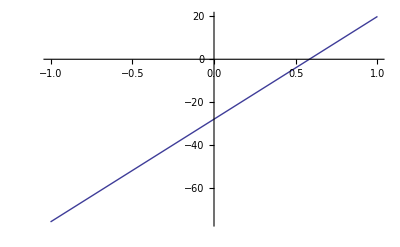

```mathematica
Plot[-28+48x,{x,-1,1}]
```

```mathematica
getRawLogA3[x_]:=Module[{xx,X,el1,el2,el3,el4},
xx=Simplify[x];
X=Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)];
el1=(a+b)/(a-b);(*=1A2*)
el2=(A+B)^2/(A^2-B^2-C^2);(*=1A1*);
el3=(A+Sqrt[B^2+C^2])/(A-Sqrt[B^2+C^2]);(*=2A1=2A2*)
el4=(A a-B b+Sqrt[X])/(A a-B b-Sqrt[X]);(*=3A2*)
Which[
Simplify[xx-el1]===0,log1A3,
Simplify[xx-1/el1]===0,-log1A3,
Simplify[xx-el2]===0,log2A3,
Simplify[xx-1/el2]===0,-log2A3,
Simplify[xx-el3]===0,log3A3,
Simplify[xx-1/el3]===0,-log3A3,
Simplify[xx-el4]===0,log4A3,
Simplify[xx-1/el4]===0,-log4A3,
True,$Failed
]];
```

```mathematica
A3v["ca"]["X-old"]=Simplify[Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)]/.repA3ca/.normA3];
A3v["ca"]["X"]=s4^2/(4(m2+s4)^2)((mγ2^2+u1p s4 -mγ2 (s4-sp))^2-4m2 s u1p (sp+u1p))
A3v["ca"]["sqrtX"]=s4/(2(m2+s4))Sqrt[((mγ2^2+u1p s4 -mγ2 (s4-sp))^2-4m2 s u1p (sp+u1p))];
Print["check: ",Simplify[(A3v["ca"]["X-old"]-A3v["ca"]["X"])/.normA3]]
Print["check: ",Simplify[(A3v["ca"]["sqrtX"]^2-A3v["ca"]["X"])/.normA3]]
A3v["cb"]["X-old"]=Simplify[Simplify[(A a - b B)^2-(A^2-B^2-C^2)(a^2-b^2)]/.repA3cb/.normA3];
A3v["cb"]["X"]=A3v["ca"]["X"];
A3v["cb"]["sqrtX"]=A3v["ca"]["sqrtX"];
Print["check: ",Simplify[(A3v["cb"]["X-old"]-A3v["cb"]["X"])/.normA3]]
```

(s4^2 (-4 m2 s u1p (sp+u1p)+(mγ2^2-mγ2 (s4-sp)+s4 u1p)^2))/(4 (m2+s4)^2)

check: 0

check: 0

check: 0

### List

#### subparts

```mathematica
psIA3aa[0,0]=psIA1[0,0];
psIA3aa[0,1]=psIA1[0,1]/.{log2A1-> log3A3aa};
psIA3aa[1,0]=psIA1[1,0];
psIA3aa[1,1]=psIA1[1,1]/.{log1A1-> log2A3aa};
psIA3aa[-1,1]=psIA1[-1,1]/.{log2A1-> log3A3aa};
psIA3aa[-2,1]=psIA1[-2,1]/.{log2A1-> log3A3aa}

psIA3bb[0,1]=psIA2b[0,1]/.{log2A2b-> log3A3bb};
psIA3bb[1,1]=psIA2b[1,1]/.{log3A2b-> log4A3bb};
psIA3bb[-1,1]=psIA2b[-1,1]/.{log2A2b-> log3A3bb};

psIA3bc[0,1]=psIA2a[0,1]/.{log2A2a-> log3A3bc};
psIA3bc[1,1]=psIA2a[1,1]/.{log3A2a-> log4A3bc};
psIA3bc[-1,1]=psIA2a[-1,1]/.{log2A2a-> log3A3bc};

psIA3ca[1,1]=2π(s4+m2)/(s4 Sqrt[(mγ2^2+u1p s4 -mγ2 (s4-sp))^2-4m2 s u1p (sp+u1p)])*log4A3ca;
psIA3cb[1,1]=2π(s4+m2)/(s4 Sqrt[(mγ2^2+u1p s4 -mγ2 (s4-sp))^2-4m2 s u1p (sp+u1p)])*log4A3cb;
```

psIA1[-2,1]

#### joint

```mathematica
psIA3[1,1,1,1]=1/(sp u1p) (psIA3ab[1,1]-psIA3cb[1,1]+psIA3aa[1,1]-psIA3ca[1,1]) + 1/(sp (sp+u1p))(-psIA3bb[1,1]+psIA3cb[1,1]-psIA3aa[1,1]+psIA3ca[1,1]-psIA3ac[1,1]+psIA3bc[1,1]);
psIA3[1,-1,1,1]=-psIA3bb[1,1]-psIA3aa[1,1]+psIA3bc[1,1]+u1p/sp(psIA3ab[1,1]-psIA3bb[1,1]-psIA3ac[1,1]+psIA3bc[1,1]);
psIA3[1,1,1,-1]=-psIA3cb[1,1]+psIA3aa[1,1]-psIA3ca[1,1]+sp/u1p(psIA3ab[1,1]-psIA3cb[1,1]+psIA3aa[1,1]-psIA3ca[1,1]);
psIA3[1,-1,1,-1]=psIA3aa[0,0]-psIA3bb[-1,1]+u1p(psIA3bb[0,1]-psIA3aa[1,0])+sp u1p psIA3bb[1,1]-psIA3ac[1,-1];
psIA3[0,1,1,1]=1/(sp+u1p)(psIA3bb[1,1]-psIA3cb[1,1]-psIA3ca[1,1]-psIA3bc[1,1]);
psIA3[1,0,1,1]=1/sp(-psIA3ab[1,1]+psIA3bb[1,1]+psIA3ac[1,1]-psIA3bc[1,1]);
psIA3[1,1,0,1]=1/(sp+u1p)(-psIA3aa[1,1]-psIA3ac[1,1]);
psIA3[1,1,1,0]=1/u1p(-psIA3ab[1,1]+psIA3cb[1,1]-psIA3aa[1,1]+psIA3ca[1,1]);
psIA3[-1,1,1,0]=psIA3bb[0,1]+psIA3aa[0,1]+u1p(psIA3cb[1,1]+psIA3ca[1,1]);
psIA3[0,-1,1,1]=-psIA3bb[0,1]+(sp+u1p)(psIA3bb[1,1]-psIA3bc[1,1]);
psIA3[0,1,1,-1]=-psIA3bb[0,1]-(sp+u1p)(psIA3cb[1,1]+psIA3ca[1,1]);
psIA3[1,-1,0,1]=-psIA3aa[1,0]-(sp+u1p)psIA3ac[1,1];
psIA3[1,-1,1,0]=psIA3bb[0,1]-psIA3aa[1,0]-u1p psIA3ab[1,1];
psIA3[1,0,-1,1]=psIA3aa[1,0]+psIA3bc[0,1]+sp psIA3ac[1,1];
psIA3[1,0,1,-1]=-psIA3bb[0,1]+psIA3aa[1,0]-sp psIA3ab[1,1];
psIA3[1,1,0,-1]=-psIA3aa[1,0]-(sp+u1p)psIA3aa[1,1];
psIA3[0,0,1,1]=-psIA3bb[1,1]+psIA3bc[1,1];
psIA3[0,1,0,1]=1/(sp+u1p)(-psIA3aa[0,1]-psIA3bc[0,1]);
psIA3[0,1,1,0]=psIA3cb[1,1]+psIA3ca[1,1];
psIA3[1,0,0,1]=psIA3ac[1,1];
psIA3[1,0,1,0]=psIA3ab[1,1];
psIA3[1,1,0,0]=psIA3aa[1,1];
psIA3[-1,0,1,0]=psIA3ab[-1,1];
psIA3[-1,1,0,0]=psIA3aa[-1,1];
psIA3[0,-1,0,1]=-psIA3aa[0,0]-(sp+u1p)psIA3bc[0,1];
psIA3[0,-1,1,0]=-psIA3aa[0,0]+psIA3cb[-1,1];
psIA3[0,0,-1,1]=psIA3aa[0,0]+psIA3bc[-1,1];
psIA3[0,0,1,-1]=psIA3aa[0,0]-psIA3bb[-1,1];
psIA3[0,1,0,-1]=-psIA3aa[0,0]-(sp+u1p)psIA3aa[0,1];
psIA3[1,-1,0,0]=psIA3aa[1,-1];
psIA3[1,0,-1,0]=psIA3ab[1,-1];
psIA3[1,0,0,-1]=psIA3ac[1,-1];
psIA3[0,0,0,1]=psIA3bc[0,1];
psIA3[0,0,1,0]=psIA3bb[0,1];
psIA3[0,1,0,0]=psIA3aa[0,1];
psIA3[1,0,0,0]=psIA3aa[1,0];
psIA3[0,0,0,0]=psIA3aa[0,0];

psIA3[-1,1,1,1]=-psIA3cb[1,1]-psIA3ca[1,1]+sp/(sp+u1p)(-psIA3bb[1,1]+psIA3cb[1,1]+psIA3ca[1,1]+psIA3bc[1,1])+1/(sp+u1p)(-psIA3aa[0,1]-psIA3bc[0,1]);
psIA3[-2,1,1,1]=-psIA3bb[0,1]-psIA3aa[0,1]+(sp-u1p)(psIA3cb[1,1]+psIA3ca[1,1])+1/(sp+u1p)(-psIA3aa[-1,1]-psIA3ac[-1,1])+sp/(sp+u1p)(psIA3aa[0,1]+psIA3bc[0,1])+sp^2/(sp+u1p)(psIA3bb[1,1]-psIA3cb[1,1]-psIA3ca[1,1]-psIA3bc[1,1]);
psIA3[-1,-1,1,1]=-psIA3ab[-1,1]+(sp+u1p)(psIA3bb[0,1]-psIA3bc[0,1])+sp(sp+u1p)(-psIA3bb[1,1]+psIA3bc[1,1]);
psIA3[-1,0,1,1]=-psIA3bb[0,1]+psIA3bc[0,1]+sp(psIA3bb[1,1]-psIA3bc[1,1]);
psIA3[-1,1,0,1]=1/(sp+u1p)(-psIA3aa[-1,1]-psIA3ac[-1,1]);
psIA3[-2,0,1,1]=-psIA3ab[-1,1]+psIA3ac[-1,1]+sp(psIA3bb[0,1]-psIA3bc[0,1])+sp^2(psIA3bb[1,1]+psIA3bc[1,1]);
psIA3[-2,1,0,1]=1/(sp+u1p)(-psIA3aa[-2,1]-psIA3ac[-2,1]);
psIA3[-1,0,0,1]=psIA3ac[-1,1];
```

### compute missing from package

#### cb 1,1

```mathematica
Module[{i},
i=Normal@Simplify@Series[PsInt0[1,1][a,b,A,B,C]/.{dDim-> 4+ϵ},{ϵ,0,0}];
Print@i;
i=i/.{Log[x_]:> getRawLogA3[x]}/.{log4A3->log4A3cb}/.repA3cb/.normA3;
Print@Simplify[i-(psIA3cb[1,1]/.normA3),Assumptions-> {sp>0,m2>0,mγ2<0,t1<0,u1<0,sp+t1+u1>0,sp+mγ2>0}];
]
```

(π Log[-(a A-b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))/(-a A+b B+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))])/(√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))

0